## Training a classifier with labeled inputs

As mentioned in the introduction, classifiers have to be trained to be functional (see the figure).

In the previous chapter we have seen how to used pre-built classifiers available in Wolfram Language. These classifiers were previously trained and allow us to do classification tasks without having to train them ourselves. 

However, in many cases there is no pre-trained classifier available and we need to use data to train our own classifier.

-Graphics-

## Training with the Classify function

Classify can be used on many types of data, including numerical, textual, sounds and images, as well as combinations of these.

Given a set {(example_i,C_i)}_(i=1)^K of labeled examples belonging to classes , the Classify function can be used to train a classifier (i.e. to provide a ClassifierFunction) in several different ways. We will use the following formats:

Classify[{example_1→ C_1,example_2→ C_2,…}] 

Classify[{example_1, example_2,…} → {C_1,C_2,…}] 

Classify[<|C_1→ {example_11, example_12,…} ,C_2→ {example_21, example_22,…}|>] 

Each example can be a single data element, a list of data elements, an association of data elements, or a Dataset object.

### Some examples

#### Example 1: Numbers to classes

Simple dataset with two classes, “A” and “B”. For instance classification of children in a certain class depending on their age

```mathematica
trainingset = {1->"A",2->"A",3.5->"B",4->"B"};
```

Use Classify to a classifier c1, i.e. a ClassifierFunction):

```mathematica
c1=Classify[trainingset]
```

ClassifierFunction[…]

Classify now a previously unseen data

```mathematica
c1[2.5]
```

A

```mathematica
c1[{0,1.4,2.7,3.2,4.8}]
```

{A,A,A,B,B}

#### Example 2: A classical machine learning example - A classifier for dogs and cats

```mathematica
trainingset = {-Graphics-->"cat",-Graphics-->"cat",-Graphics-->"cat",-Graphics-->"cat",
-Graphics-->"dog",-Graphics-->"dog",-Graphics-->"dog",-Graphics-->"dog"};
```

```mathematica
cDC=Classify[trainingset]
```

ClassifierFunction[…]

We now check if it classifies some dogs and cats

```mathematica
prediction=cDC[{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}]
```

{dog,cat,dog,cat,dog,cat,cat,cat,dog}

```mathematica
TableForm[Transpose[Join[{{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},prediction}]]]
```

-Graphics- | dog
-Graphics- | cat
-Graphics- | dog
-Graphics- | cat
-Graphics- | dog
-Graphics- | cat
-Graphics- | cat
-Graphics- | cat
-Graphics- | dog

Not too bad.

#### Example 3: Train a classifier to provide image labels for text data

```mathematica
cText=Classify[{"a green object"-> -Graphics-,"a yellow object"-> -Graphics-,"the star is nice"-> -Graphics-,"the car is green"-> -Graphics-,"a little ellipse"-> -Graphics-, "yellow light"-> -Graphics-}]
```

ClassifierFunction[…]

```mathematica
cText[{"The axis of the ellipse","a yellow car came","she is a raising star","a yellow ellipse","a yellow ellipse intersecting a star","a green ellipse intersecting a star"}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

#### Example 4: Win/Lose game

Consider, for instance a game in which you win a prize if you get an object from the “Win” class or lose if you get an object from the “Lose” class. All you know is some of the objects in each class. You don’t know all! Our aim is to train a classifier to determine if any of the objects I can get correspond to the Win or the Lose type

In order to train a classifier based on the data in the figure, we first need to decide how each object will be described. Let us describe each example by its shape and colour (size and other features will be neglected). 

This demonstrates that Examples can consist of a list of data elements.

```mathematica
trainingset=<|"Win"-> {{"rectangle","blue"},{"rectangle","blue"},{"circle","blue"},{"star","blue"},{"ellipse","yellow"},{"ellipse","yellow"},{"ellipse","green"},{"ellipse","red"}},"Lose"->{{"circle","red"},{"ellipse","yellow"},{"cloud","green"},{"star","yellow"},{"lightning","green"},{"triangle","red"}} |>;
```

```mathematica
cWL=Classify[trainingset]
```

ClassifierFunction[…]

You now get objects that have never seen before:

According to our classifier function, do they belong to the “Win” or “Lose” class?

```mathematica
cWL[{"heart","blue"}]
```

Win

```mathematica
cWL[{"circle","yellow"}]
```

Lose

```mathematica
cWL[{"cloud","blue"}]
```

Lose

```mathematica
cWL[{"star","red"}]
```

Lose

```mathematica
cWL[{"arrow","orange"}]
```

Lose

```mathematica
cWL[{"a","b"}]
```

Win

### Probabilities of inferred classes

The classifier functions obtained with the Classify superfunction predict a definite output for any entry. Since classification is applied to unseen examples, however, in many cases it is difficult to say that they definitely belong to only one class. 

Let us look at the probabilities of each class in the examples studied above

#### Example 1

Probabilities for some values of the feature:

```mathematica
c1[2.5,"Probabilities"]
```

<|A→0.978459,B→0.0215408|>

```mathematica
c1[{0,1.4,2.7,3.2,4.8},"Probabilities"]
```

{<|A→1.,B→2.09×10^-19|>,<|A→1.,B→7.12503×10^-10|>,<|A→0.663819,B→0.336181|>,<|A→0.000777363,B→0.999223|>,<|A→9.92008×10^-15,B→1.|>}

Plot the probability that the class of an example is "A" as a function of the feature:

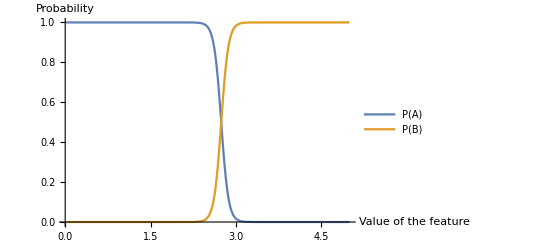

```mathematica
Plot[{c1[x,"Probability"->"A"],c1[x,"Probability"->"B"]},{x,0,5},AxesLabel->{"Value of the feature","Probability"},PlotLegends->{"P(A)","P(B)"}]
```

```mathematica
FindRoot[c1[x,"Probability"->"A"]==c1[x,"Probability"->"B"],{x,2}]
```

ClassifierFunction::mlincfttp: Incompatible variable type (Numerical) and variable value (x).

{x→2.74339}

```mathematica
c1[2.743394708077354,"Probability"->"B"]
```

0.5

#### Example 2

Probability that any image is classified as cat or dog

```mathematica
predictionP=cDC[{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},"Probabilities"]
```

{<|cat→6.07417×10^-132,dog→1.|>,<|cat→1.,dog→6.07123×10^-68|>,<|cat→3.42787×10^-180,dog→1.|>,<|cat→1.,dog→1.96761×10^-58|>,<|cat→5.65228×10^-90,dog→1.|>,<|cat→1.,dog→1.78944×10^-46|>,<|cat→0.990698,dog→0.00930234|>,<|cat→1.,dog→4.19889×10^-12|>,<|cat→9.77418×10^-262,dog→1.|>}

```mathematica
TableForm[Transpose[{{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},predictionP}]]
```

-Graphics- | <|cat→0.,dog→1.|>
-Graphics- | <|cat→0.,dog→1.|>
-Graphics- | <|cat→0.,dog→1.|>
-Graphics- | <|cat→1.,dog→2.05414×10^-14|>
-Graphics- | <|cat→0.,dog→1.|>
-Graphics- | <|cat→9.81479×10^-305,dog→1.|>
-Graphics- | <|cat→0.,dog→1.|>
-Graphics- | <|cat→1.,dog→3.24892×10^-190|>
-Graphics- | <|cat→0.,dog→1.|>

#### Example 3

```mathematica
cText[{"The axis of the ellipse","a yellow car came","she is a raising star","a yellow ellipse","a yellow ellipse intersecting a star","a green ellipse intersecting a star"},"Probabilities"]
```

{<|-Graphics-→0.87682,-Graphics-→0.12318|>,<|-Graphics-→0.412248,-Graphics-→0.587752|>,<|-Graphics-→0.10113,-Graphics-→0.89887|>,<|-Graphics-→0.431673,-Graphics-→0.568327|>,<|-Graphics-→0.0941159,-Graphics-→0.905884|>,<|-Graphics-→0.978601,-Graphics-→0.0213995|>}

#### Example 4

```mathematica
cWL[{{"heart","blue"},{"circle","yellow"},{"cloud","blue"},{"star","red"},{"arrow","orange"},{"a","b"}},"Probabilities"]
```

{<|Lose→0.0894863,Win→0.910514|>,<|Lose→0.947432,Win→0.0525683|>,<|Lose→0.262875,Win→0.737125|>,<|Lose→0.861445,Win→0.138555|>,<|Lose→0.974954,Win→0.0250455|>,<|Lose→0.00141304,Win→0.998587|>}

## Evaluating the performance of a classifier using test data

### Measures of model performance

We now introduce measures to evaluate the performance of a classification model. This will be done using the dog/cat classifier obtained in Example 2. 

Using examples of images of dogs and cats, we saw that the classifier is not able to properly classify some of them. By doing this, we simply used a test dataset with categories identified by ourselves, i.e. by humans who have seen many more cats and dogs than our classifier.

Warning: The results may vary depending on the Mathematica version you use. Comments here are based on Mathematica 11 but they may be different for later versions.

Let us then define a test dataset based on the unseen images:

```mathematica
testDC={-Graphics--> "dog",-Graphics--> "cat",-Graphics--> "dog",-Graphics--> "cat",-Graphics--> "dog",-Graphics-->"cat",-Graphics--> "dog",-Graphics-->"cat",-Graphics-->"dog"};
```

#### Accuracy and Error

```mathematica
8/9//N
```

0.888889

The accuracy of a classifier is the proportion of examples in the test set that are correctly classified.

In testDC there are 9 images and 8 of them were correctly classified with cDC:

Accuracy = 8/9

The error is the proportion of examples in the test set that are incorrectly classified:

Error = 1 - Accuracy

#### Pre-built measures of model performance

The accuracy of a classifier is the most basic measure of performance. However, performance is a broad concept and there are many other measures that can be used to quantify performance.

The function ClassifierMeasurements offers a wide range of measures to evaluate the performance of a classifier on a test dataset:

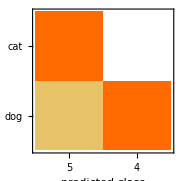
Classifier Measurements
Classifier method | LogisticRegression
Number of test examples | 9
Accuracy | (89.11.) %
Accuracy baseline | (56.18.) %
Geometric mean of probabilities | 0.595 ± 0.32
Mean cross entropy | 0.519 ± 0.52
Single evaluation time | 62.1 ms/example
Batch evaluation speed | 16.6 examples/s
-Graphics- |

```mathematica
cmDC=ClassifierMeasurements[cDC,testDC]
```

```mathematica
prediction=cDC[{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}]
```

{dog,cat,dog,cat,dog,cat,cat,cat,dog}

The performance measures available for the dog/cat classifier are the following

```mathematica
cmDC["Properties"]
```

{Accuracy,AccuracyBaseline,AccuracyRejectionPlot,AreaUnderROCCurve,BatchEvaluationTime,BestClassifiedExamples,CalibrationCurve,CalibrationData,ClassifierFunction,ClassMeanCrossEntropy,ClassRejectionRate,CohenKappa,ConfusionDistribution,ConfusionFunction,ConfusionMatrix,ConfusionMatrixPlot,CorrectlyClassifiedExamples,DecisionUtilities,Error,EvaluationTime,Examples,F1Score,FalseDiscoveryRate,FalseNegativeExamples,FalseNegativeNumber,FalseNegativeRate,FalsePositiveExamples,FalsePositiveNumber,FalsePositiveRate,GeometricMeanProbability,IndeterminateExamples,LeastCertainExamples,Likelihood,LinearCalibrationCurve,LogLikelihood,MatthewsCorrelationCoefficient,MeanCrossEntropy,MeanDecisionUtility,MisclassifiedExamples,MostCertainExamples,NegativePredictiveValue,Perplexity,Precision,Probabilities,ProbabilityHistogram,Properties,Recall,RejectionRate,Report,ROCCurve,ROCData,ScottPi,Specificity,TopConfusions,TrueNegativeExamples,TrueNegativeNumber,TruePositiveExamples,TruePositiveNumber,WorstClassifiedExamples}

The accuracy and error of the dog/cat classifier can be readily obtained from the classifier measurements function:

```mathematica
cmDC["Accuracy"]
```

0.888889

```mathematica
cmDC["Error"]
```

0.111111

#### Confusion matrix

The confusion matrix (or error matrix) is a table that gives a visualisation of the performance of an algorithm.

Before defining the confusion matrix, let us consider a test dataset of n_e instances that belong to K classes, {C_i}_(i=1)^K. 

Let us split the set of examples into two subsets: examples in class C_i and those (Not C_i) that belong to any other class.

-Graphics-

We now apply a classifier to these examples. 

Question: Is an example assigned to class C_i? 

-Graphics-
The answer can be positive (P, if “yes”) or negative (N, if “no”). 
If we take into account the true class of each example, there are 4 possibilities:

True positive: Belongs to class C_i and it is correctly assigned to C_i.
True negative: Does not belong to C_i and is not assigned to C_i.
False positive: Does not belong to C_i but it is incorrectly assigned to C_i.
False negative: Belongs to C_i but it is not assigned to C_i.

The confusion matrix summarises the number of true positive (TP_i), true negative (TN_i), false positive (FP_i) and false negative (FN_i) instances:
-Graphics-

Here, 
|C_i| and |Not C_i| are the number of instances with true class C_i and other classes, respectively.
P_i and N_i are the number of instances classified, respectively,  as positive and negative with reference to class C_i.

Warning: Note that in the literature one can find definitions of the confusion matrix that are the transpose of the matrix defined in Wolfram Language (i.e. in these works, the, the actual class corresponds to columns and the predicted class to rows).

For the cat/dog classifier, the confusion matrix looks like this:

```mathematica
cmDC["ConfusionMatrixPlot"]
```

-Graphics-

The numbers TP, TN, FP and FN for each class can be easily obtained from the ClassifierMeasurements function :

```mathematica
cmDC["TruePositiveNumber"]
```

<|cat→4,dog→4|>

```mathematica
cmDC["TrueNegativeNumber"]
```

<|cat→4,dog→4|>

```mathematica
cmDC["FalsePositiveNumber"]
```

<|cat→1,dog→0|>

```mathematica
cmDC["FalseNegativeNumber"]
```

<|cat→0,dog→1|>

#### Rates - Evaluation metrics derived from the confusion matrix

The accuracy and error can be formally expressed in terms of TP_i and TN_i as follows

	Accuracy = (TP_i+TN_i)/Total

	Error = 1-Accuracy 

Remark 1: Note that, in fact, Accuracy and Error do not depend on the class i we chose to specify TP_i and TN_i. Indeed, the sum TP_i + TN_i gives the number of instances in the test dataset that are correctly classified to any class and this is independent of the specific class i chosen to do the calculation.

Remark 2: TP_i + TN_i is the sum of the diagonal elements of the confusion matrix.

One can define many rates to interpret the numbers in the confusion matrix. Here I explain some but one can define more (for instance, see more examples in Wikipedia).

True positive rate for class C_i (or recall or sensitivity): Fraction of elements of class C_i that  are correctly attributed to class C_i

	TPR_i=TP_i/(|C_i|)=TP_i/(TP_i+FN_i)

```mathematica
cmDC["TruePositiveRate"]
```

<|cat→1.,dog→0.2|>

```mathematica
cmDC["Recall"]
```

<|cat→1.,dog→0.2|>

```mathematica
cmDC["Sensitivity"]
```

<|cat→1.,dog→0.2|>

True negative rate for class C_i (or specificity): Fraction of times an example in Not C_i is not classified as C_i.

	TNR_i = Specificity_i=TN_i/(|Not C_i|)=TN_i/(TN_i+FP_i)

```mathematica
cmDC["TrueNegativeRate"]
```

<|cat→0.2,dog→1.|>

```mathematica
cmDC["Specificity"]
```

<|cat→0.2,dog→1.|>

Positive predictive value for class C_i (or precision): Fraction of times a prediction for class C_i is correct

	PPV_i=Precision_i=TP_i/P_i=TP_i/(TP_i+FP_i)

```mathematica
cmDC["Precision"]
```

<|cat→0.5,dog→1.|>

```mathematica
cmDC["PositivePredictiveValue"]
```

<|cat→0.5,dog→1.|>

Negative predictive value for class C_i : Fraction of times a prediction for not Not C_i is correct.

	NPV_i = TN_i/N_i=TN_i/(TN_i+FN_i)

```mathematica
cmDC["NegativePredictiveValue"]
```

<|cat→1.,dog→0.5|>

False positive rate for class C_i (or false alarm): Fraction of elements in Not C_i that are attributed to class  C_i 

	FPR_i=FP_i/(|Not C_i|)=FP_i/(TN_i+FP_i)

```mathematica
cmDC["FalsePositiveRate"]
```

<|cat→0.8,dog→0.|>

Remark: Which of these measures is best depends on the application we are dealing with. For example, if you are testing for coronavirus infection, you don’t want to miss positive cases and you want a small number of false negatives. In contrast, false positives, might not be so damaging.

In general, it is good to look at several measures of performance.

### ROC (Receiver Operating Characteristic)

The ROC curve is yet another way of quantifying how well a classifier works. If we wanted to compare several trained classifiers, the ROC curve is a good way to do that. 

Before looking at ROC curves, we define the ROC space where the ROC curve is plotted.

#### ROC space

Space defined by the TPR (recall or sensitivity) against the FPR (false alarm) of classifiers. Since TPR, FPR ∈[0,1], this is the space [0,1]×[0,1] .

Remember: TPR_i=TP_i/(|C_i|)=TP_i/(TP_i+FN_i)  and FPR_i=FP_i/(|Not C_i|)=FP_i/(TN_i+FP_i).

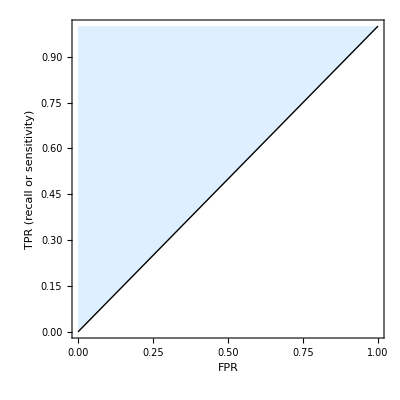

```mathematica
Plot[x,{x,0,1},PlotRange->{{0,1},{0,1}}, PlotStyle->{Black,Thick}, AspectRatio->1,Frame->True,FrameLabel->{"FPR","TPR (recall or sensitivity)"},LabelStyle->Directive[Medium],Filling->Top,FillingStyle->LightBlue]
```

#### Two tasks for you:

Task 1: To get a feeling about the meaning of this representation, calculate the TPR and FPR for the following examples and see where they fall in the the ROC space.

Example A

```mathematica
confusionA={{" ","Pred. C", "Pred. (Not C)"},{"Actual C",70,30},{"Not C",20,80}};
exampleA=Grid[confusionA,Frame->All]
```

| Pred. C | Pred. (Not C)
Actual C | 70 | 30
Not C | 20 | 80

Example B

```mathematica
confusionB={{" ","Pred. C", "Pred. (Not C)"},{"Actual C",20,80},{"Not C",70,30}};
exampleB=Grid[confusionB,Frame->All]
```

| Pred. C | Pred. (Not C)
Actual C | 20 | 80
Not C | 70 | 30

Example C

```mathematica
confusionC={{" ","Pred. C", "Pred. (Not C)"},{"Actual C",80,20},{"Not C",80,20}};
exampleC=Grid[confusionC,Frame->All]
```

| Pred. C | Pred. (Not C)
Actual C | 80 | 20
Not C | 80 | 20

```mathematica
confusionD={{" ","Pred. C", "Pred. (Not C)"},{"Actual C",70,30},{"Not C",40,160}};
exampleD=Grid[confusionD,Frame->All]
```

| Pred. C | Pred. (Not C)
Actual C | 70 | 30
Not C | 40 | 160

(The answer button only works in my computer ;) ). Sorry...

```mathematica
Button["Answer",NotebookOpen["C:\\Users\\s05fp2\\Documents\\Teaching\\MSc_Data_Science\\2020-2021\\Lectures\\Ch3_Supervised_Learning_Classification_Additional\\Ch3-2_ML_Classify_Notebook_Task1_TPR_FPR.nb"]]
```

Answer

Task 2: Show that any point along the diagonal line in the ROC space corresponds to a classifier that randomly guesses if an instance belongs to class C or not. Can you give a meaning to the specific point predicted by a classifier along the diagonal? (hint: Thinking in terms of random sampling and probabilities can help).

#### ROC curve

Many classifiers yield a score for each instance. For example, a probability that each instance belongs to a certain class. 

Suppose there is a threshold, τ, in the classification algorithm that determine whether you have class C_i or class “Not C_i”  (i.e. any other class different to C_i)

-Graphics-

Example: Let us assume C_i =cat. If the threshold (i.e. a numerical value) is below the probability of classification of an example (e.g. the image of a cat or a dog) then the example is classified as a cat. 
The image could be the one of a dog. In this case, this would contribute to the FPR for cats.

Mathematically: Let C_i =cat. Predicted class for an image I will be “cat” if P_classifier(I =cat) > τ.

Perfect prediction for class C_i: possible if for some value of τ, TPR_i = 1 and FPR_i=0, i.e. when all the elements in class C_i are correctly classified.
The point TPR_i = 0 and FPR_i=0 can be achieved by any system for large enough threshold (all instances classified as Not C_i)
The point TPR_i = 1 and FPR_i=1 can be achieved by any system for low enough threshold (everything classified as positive but many false positive)

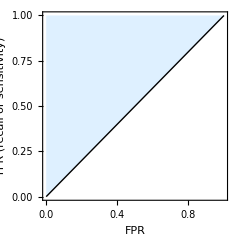

```mathematica
Plot[x,{x,0,1},PlotRange->{{0,1},{0,1}}, PlotStyle->{Black,Thick}, AspectRatio->1,Frame->True,FrameLabel->{"FPR","TPR (recall or sensitivity)"},LabelStyle->Directive[Medium],Filling->Top,FillingStyle->LightBlue]
```

The ROC curve for elements in class  C_i is a plot of TPR against FPR as the discriminatory threshold varies. 

The faster TPR increases for increasing FPR, the better.

Intuitive meaning of the ROC curve: It shows the ability of a classifier to rank the positive instances for a class relative to the negative instances for that class. A classifier that is able to rank all positives for the class under consideration with a higher score than all negatives, is perfect in the ROC curve sense.

Remark: Note that a perfect ranking for a class does not imply an overall TPR = 1 for that class (for instance, see below the case for cats). 

Here, you will see two examples to illustrate the functioning of ROC curves (you will do one of them yourselves). 

If you are interested in more examples and further details, the following paper is good (Available in MyAberdeen in folder Additional materials - Papers, etc):

Fawcett T. 2006 An introduction to ROC analysis. Pattern Recognit. Lett. 27, 861–874. (doi:10.1016/j.patrec.2005.10.010)

#### A ROC curve example:

Consider something similar to the Example 1 shown above, i.e. assignment of numbers to classes A and B, but we use a slightly larger training dataset.

The training (synthetic) data is:

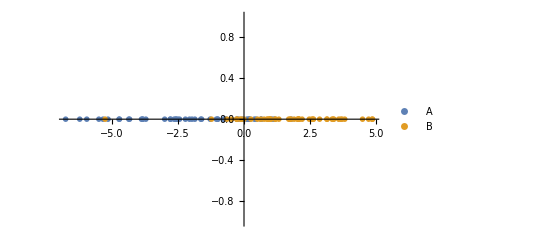

```mathematica
trainclassA={-4.7239,0.644997,-2.44533,-0.773269,-2.80093,1.13677,-5.35028,1.05545,-2.58404,-5.50499,-2.2223,-6.7659,0.217003,-2.65282,-1.86305,-0.268906,-6.23136,0.654171,-1.28425,-3.84159,-0.218235,-0.997377,0.10369,-2.58301,1.79419,-2.51586,-0.996947,-0.764041,-3.84564,-0.675974,-1.60871,-1.97262,-3.88967,-3.72365,0.392733,-0.714363,-3.00814,-4.3406,-1.04839,-5.15876,-0.0644995,-1.63869,0.457775,-2.06747,-5.96453,0.164844,-4.37046,-4.73958,0.2001,-2.78308};
trainclassB={3.34109,-0.2784,3.5913,4.72819,0.98379,1.32203,4.49713,0.762486,1.02798,1.69669,1.78772,-5.26952,3.71933,-0.477114,2.47588,2.61623,0.265969,1.19155,-0.147187,3.40941,2.0528,0.969542,1.7449,2.0903,2.02585,2.0721,0.873215,4.87697,0.965366,0.641487,3.67131,-1.23224,-0.266107,2.63745,0.901371,3.1432,1.18738,2.20526,2.86737,-0.00343949,3.15468,4.86185,2.08779,2.57229,0.51376,3.82214,3.38325,-0.649899,-0.0982375,1.90127};
n=Length[trainclassA];
ListPlot[{Transpose[{trainclassA,Table[0,{i,1,n}]}],Transpose[{trainclassB,Table[0,{i,1,n}]}]},PlotMarkers->{"OpenMarkers", Medium},PlotLegends->{"A","B"}]
```

Aside: These data are normally distributed random variable (to be covered in Chapter 4). The can be generated as follows:

```mathematica
n=50;
μ=2;
σ=2;
trainclassArv=RandomVariate[NormalDistribution[-μ,σ],n];
trainclassBrv=RandomVariate[NormalDistribution[μ,σ],n];
```

Let us train a classifier using the data:

```mathematica
c=Classify[Flatten[{Table[trainclassA[[i]]->"A",{i,1,n}],Table[trainclassB[[i]]->"B",{i,1,n}]}],Method->"LogisticRegression"]
```

ClassifierFunction[…]

Probability of class “A” as a function of the feature, x:

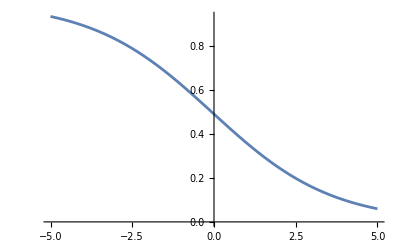

```mathematica
Plot[c[x,"Probability"->"A"],{x,-5,5}]
```

We also define a test dataset using the same procedure as for the training set (i.e. normally distributed random variable):

```mathematica
ntest=10;
testclassA={0.484849,-2.26168,-2.64966,-2.47983,-2.10977,0.471449,-1.01995,-2.97273,-0.652767,-2.69489};
testclassB={0.083667,1.17197,0.690443,1.53969,6.39469,2.79436,2.61048,3.64717,4.49088,6.06011};
```

```mathematica
testdata=Flatten[{Table[testclassA[[i]]->"A",{i,1,ntest}],Table[testclassB[[i]]->"B",{i,1,ntest}]}];
```

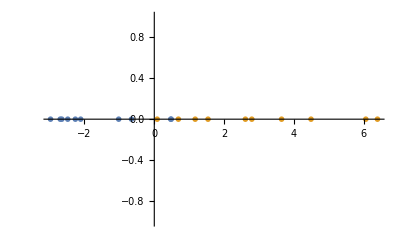

```mathematica
ListPlot[{Transpose[{testclassA,Table[0,{i,1,ntest}]}],Transpose[{testclassB,Table[0,{i,1,ntest}]}]},PlotMarkers->{"OpenMarkers", Medium}]
```

Let us obtain a classifier measurements object based on the trained classifier and test data:

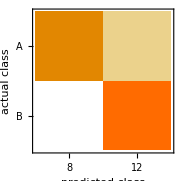
Classifier Measurements
Classifier method | LogisticRegression
Number of test examples | 20
Accuracy | (90.7.) %
Accuracy baseline | (50.11.) %
Geometric mean of probabilities | 0.715 ± 0.039
Mean cross entropy | 0.336 ± 0.054
Single evaluation time | 1.79 ms/example
Batch evaluation speed | 1.07 examples/ms
-Graphics- |

```mathematica
cm=ClassifierMeasurements[c,testdata]
```

ROC curves. An association with the curve for each class.

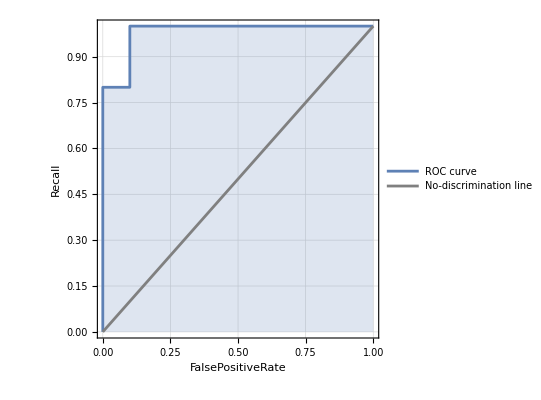
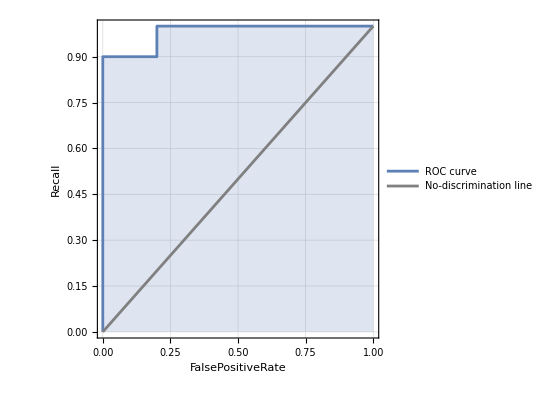
<|A→-Graphics-,B→-Graphics-|>

```mathematica
cm["ROCCurve"]
```

The ROC curve for the class A is

```mathematica
cm["ROCCurve"][[1]]
```

-Graphics-

Area under the ROC curve: It summarises the ROC curve in terms of a numerical value. Quantifies the ability of the classifier to rank the positive instances relative to the negative instances. 

The area is between 0 (worst) and 1 (best ranking of positives).

```mathematica
cm["AreaUnderROCCurve"]
```

<|A→0.98,B→0.98|>

```mathematica
cm["Probabilities"]
```

{0.426002,0.767917,0.803409,0.7884,0.752857,0.427787,0.627332,0.829709,0.579556,0.807268,0.51995,0.661982,0.601105,0.705217,0.971099,0.82565,0.810771,0.882802,0.922615,0.965525}

#### Explanation of the ROC curve

We can build a table with the instances sorted in decreasing order of the probability that they are classified as class “A”:

```mathematica
(* First sort the examples in the test dataset in decreasing order of probability to be classified as A *)
probc=c[testdata[[All,1]],"Probability"->"A"];
sortedProbabilities=Reverse[Sort[probc]];
sortedTestclass=testdata[[Reverse[Ordering[probc]]]][[All,2]];
sortedPredictedclass=c[testdata[[All,1]]][[Reverse[Ordering[probc]]]];

{TableForm[Transpose[{sortedTestclass,sortedProbabilities}],TableHeadings->{{},{"True class","Probability to be A"}}],cm["ROCCurve"][[1]]}//TableForm
```

| True class | Probability to be A
 | A | 0.829709
 | A | 0.807268
 | A | 0.803409
 | A | 0.7884
 | A | 0.767917
 | A | 0.752857
 | A | 0.627332
 | A | 0.579556
 | B | 0.48005
 | A | 0.427787
 | A | 0.426002
 | B | 0.398895
 | B | 0.338018
 | B | 0.294783
 | B | 0.189229
 | B | 0.17435
 | B | 0.117198
 | B | 0.0773853
 | B | 0.0344746
 | B | 0.0289013
-Graphics-

As we move down the table, we first find some TP for class A that explain the vertical line at the beginning of the curve. As we proceed further, we will typically find some B that scored higher than some A instances. These give horizontal bits of the curve as they contribute to FNR for A.

#### Task for you

Task 3: Study the ROC curve for the classifier of cats and dogs studied in Example 2 above.

### Other useful measures of classifier performance

#### Best/worst classified, top confusions

```mathematica
testDC
```

{-Graphics-→dog,-Graphics-→cat,-Graphics-→dog,-Graphics-→cat,-Graphics-→dog,-Graphics-→cat,-Graphics-→dog,-Graphics-→cat,-Graphics-→dog}

```mathematica
cmDC["Properties"]
```

{Accuracy,AccuracyBaseline,AccuracyRejectionPlot,AreaUnderROCCurve,BatchEvaluationTime,BestClassifiedExamples,CalibrationCurve,CalibrationData,ClassifierFunction,ClassMeanCrossEntropy,ClassRejectionRate,CohenKappa,ConfusionDistribution,ConfusionFunction,ConfusionMatrix,ConfusionMatrixPlot,CorrectlyClassifiedExamples,DecisionUtilities,Error,EvaluationTime,Examples,F1Score,FalseDiscoveryRate,FalseNegativeExamples,FalseNegativeNumber,FalseNegativeRate,FalsePositiveExamples,FalsePositiveNumber,FalsePositiveRate,GeometricMeanProbability,IndeterminateExamples,LeastCertainExamples,Likelihood,LinearCalibrationCurve,LogLikelihood,MatthewsCorrelationCoefficient,MeanCrossEntropy,MeanDecisionUtility,MisclassifiedExamples,MostCertainExamples,NegativePredictiveValue,Perplexity,Precision,Probabilities,ProbabilityHistogram,Properties,Recall,RejectionRate,Report,ROCCurve,ROCData,ScottPi,Specificity,TopConfusions,TrueNegativeExamples,TrueNegativeNumber,TruePositiveExamples,TruePositiveNumber,WorstClassifiedExamples}

```mathematica
cmDC["WorstClassifiedExamples"]
```

{-Graphics-→cat,-Graphics-→cat,-Graphics-→cat,-Graphics-→dog,-Graphics-→dog,-Graphics-→dog,-Graphics-→dog,-Graphics-→cat,-Graphics-→dog}

```mathematica
Keys[testDC]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
cmDC["TopConfusions"]
```

{cat→dog}

#### Classifier report

One can easily obtain a panel summarising the main measurements of a classifier:

```mathematica
cmDC["Report"]
```

Classifier Measurements
Classifier method | LogisticRegression
Number of test examples | 9
Accuracy | (89.11.) %
Accuracy baseline | (56.18.) %
Geometric mean of probabilities | 0.0239 ± 0.5
Mean cross entropy | 3.73 ± 3.7
Single evaluation time | 67.8 ms/example
Batch evaluation speed | 14.7 examples/s
-Graphics- |

## Classification Methods - and overview

There are many algorithms to do supervised classification of classify data. 

Classify can handle the following methods:

“DecisionTree”	classify using a decision tree

"GradientBoostedTrees"	classify using an ensemble of trees trained with gradient boosting

"LogisticRegression"	classify using probabilities from linear combinations of features

"Markov"	classify using a Markov model on the sequence of features (only for text, bag of token, etc.)

"NaiveBayes"	classify by assuming probabilistic independence of features

"NearestNeighbors"	classify from nearest neighbor examples

"NeuralNetwork"	classify using an artificial neural network

"RandomForest"	classify using Breiman–Cutler ensembles of decision trees

"SupportVectorMachine"	classify using a support vector machine

We will see how some of these methods work in forthcoming sessions.

### If no method is specified in Classify - Cost function

#### The loss (or cost) function, J

The loss (or cost) function, J, quantifies the difference between the data and the trained classified. In other words, it tells us how well the classifier predicts the data. In particular, in the training process J measures the similarity of the trained model and the data used for training. 

Remark: Obtaining J=0 means that the model fits perfectly the training data. This is not necessarily good! Indeed, this might be a signature of overfitting: The model might fit very well our specific training dataset but might give a poor prediction for new data that was not in the training dataset. What you want is not a model that gives J=0 during training but instead a model that gives good predictions for previously unseen data.

#### Which model?

If no method is specified, the function Classify tries several methods and shows the results for the one with the smallest cost function. 

If the dataset is large, i.e. if there are many instances with many features, Wolfram Language will look at the cost function for several methods using a small set of instances first. The method or methods that perform better for the small dataset are then applied to the complete dataset.

The cost function (or loss function) measures the closeness of the trained model to the data. The higher the cost, the poorer the fit of the model to the data

For instance, the classifier trained in example used to illustrate the ROC curve  uses Random forest method:

```mathematica
Length[trainclassA]
```

50

```mathematica
trainingROC=Flatten[{Table[trainclassA[[i]]->"A",{i,1,n}],Table[trainclassB[[i]]->"B",{i,1,n}]}];
c=Classify[trainingROC]
```

ClassifierFunction[…]

```mathematica
Information[c]
```

Classifier information
Data type | Numerical
Classes | ,,AB
Accuracy | (79.4.) %
Method | NaiveBayes
Single evaluation time | 2.63 ms/example
Batch evaluation speed | 96.1 examples/ms
Loss | 0.419 ± 0.056
Model memory | 241. kB
Training examples used | 100 examples
Training time | 1.25 s
 |

### The learning curve

The learning curve shows the cost as a function of the number of instances used for training.

```mathematica
Information[c,"LearningCurve"]
```

### Information on classifiers

In order to see all the information available for a trained classifier, we use the Information function as follows:

```mathematica
Information[c,"Properties"]
```

{AcceptanceThreshold,Accuracy,AnomalyDetector,BatchEvaluationSpeed,BatchEvaluationTime,Calibrated,Classes,ClassNumber,ClassPriors,EvaluationTime,ExampleNumber,FeatureExtractor,FeatureNames,FeatureNumber,FeatureTypes,FunctionMemory,FunctionProperties,IndeterminateThreshold,LearningCurve,MaxTrainingMemory,MeanCrossEntropy,Method,MethodDescription,MethodOption,MethodParameters,MissingSynthesizer,PerformanceGoal,Properties,TrainingClassPriors,TrainingTime,UtilityFunction}

Remark: The set of properties depends on the specific method used for classification.

The specific loss function used depends on the method.

The loss function used in classifier c is based on the cross entropy (we will explicitly define it when looking at logistic regression)

```mathematica
Information[c,"MeanCrossEntropy"]
```

0.420.06

### How to specify the method to be used

Classify[{example_1→ C_1,example_2→ C_2,…}, Method→ ”Methods name” ] 

For instance, one could force the Logistic Regression or Nearest Neighbours methods in Example 1:

```mathematica
cLR=Classify[trainingROC,Method->"LogisticRegression"]
```

ClassifierFunction[…]

```mathematica
cRF=Classify[trainingROC,Method->"RandomForest"]
```

ClassifierFunction[…]

```mathematica
Information[{cLR,cRF}]
```

{Classifier information
Data type | Numerical
Classes | ,,AB
Accuracy | (81.6.) %
Method | LogisticRegression
Single evaluation time | 2.74 ms/example
Batch evaluation speed | 101. examples/ms
Loss | 0.551 ± 0.031
Model memory | 162. kB
Training examples used | 100 examples
Training time | 1.33 s
 | ,Classifier information
Data type | Numerical
Classes | ,,AB
Accuracy | (80.6.) %
Method | RandomForest
Single evaluation time | 8.23 ms/example
Batch evaluation speed | 9.7 examples/ms
Loss | 0.54 ± 0.091
Model memory | 201. kB
Training examples used | 100 examples
Training time | 548. ms
 | }

As expected, the loss is a bit higher for cLR (Logistic Regression) than for cRF (Random Forest), this is why Mathematica selected random forest as the best method for this particular dataset.

Note also that the time to train a classifier depends on the method.

## Example: Classifying iris plants

### Introduction

Data Set Information:

This is perhaps the best known database to be found in the pattern recognition literature. Fisher’s paper is a classic in the field and is referenced frequently to this day. The data set contains 3 classes of 50 instances each, where each class refers to a type of iris plant. 

Original paper:

FISHER, R. A. (1936). THE USE OF MULTIPLE MEASUREMENTS IN TAXONOMIC PROBLEMS. Annals of Eugenics, 7(2), 179–188. https://doi.org/10.1111/j.1469-1809.1936.tb02137.x

Predicted attribute: class of iris plant.

This data differs from the data presented in Fishers article (identified by Steve Chadwick, spchadwick@espeedaz.net ). The 35th sample should be: 4.9,3.1,1.5,0.2, “Iris-setosa” where the error is in the fourth feature. The 38th sample: 4.9,3.6,1.4,0.1, “Iris-setosa” where the errors are in the second and third features.

Attribute Information:

1. sepal length in cm
2. sepal width in cm
3. petal length in cm
4. petal width in cm
5. class:
-- Iris Setosa
-- Iris Versicolour
-- Iris Virginica

-Graphics-

See more information at https://archive.ics.uci.edu/ml/datasets/iris (press here)

#### Obtaining the data

We will use the data from the UCI Machine Learning Repository:

```mathematica
data1=Import["https://archive.ics.uci.edu/ml/machine-learning-databases/iris/iris.data"];
(*data=Import["/home/s05fp2/Teaching/MSc_Data_Science/Data/Iris_uci/iris.dat"]*)
```

```mathematica
(* Local file *)
(*data1=Import["C:\\Users\\s05fp2\\Documents\\Teaching\\MSc_Data_Science\\Data\\Iris_uci\\iris.dat"];*)
```

Another possible way to get the data is with the following instruction:

irisDataUCI2 =ExampleData[{“MachineLearning”,”FisherIris”},”Data”];

Note that the format of the data in this case is different to that from UCI and the instructions used below to manipulate the data should be modified to adapt to the format.

The data is the same as that from UCI. Only the name of the classes changes.

Anyway, let us explore the data from UCI:

```mathematica
data1
```

{{5.1,3.5,1.4,0.2,Iris-setosa},{4.9,3.,1.4,0.2,Iris-setosa},{4.7,3.2,1.3,0.2,Iris-setosa},{4.6,3.1,1.5,0.2,Iris-setosa},{5.,3.6,1.4,0.2,Iris-setosa},{5.4,3.9,1.7,0.4,Iris-setosa},{4.6,3.4,1.4,0.3,Iris-setosa},{5.,3.4,1.5,0.2,Iris-setosa},{4.4,2.9,1.4,0.2,Iris-setosa},{4.9,3.1,1.5,0.1,Iris-setosa},{5.4,3.7,1.5,0.2,Iris-setosa},{4.8,3.4,1.6,0.2,Iris-setosa},{4.8,3.,1.4,0.1,Iris-setosa},{4.3,3.,1.1,0.1,Iris-setosa},{5.8,4.,1.2,0.2,Iris-setosa},{5.7,4.4,1.5,0.4,Iris-setosa},{5.4,3.9,1.3,0.4,Iris-setosa},{5.1,3.5,1.4,0.3,Iris-setosa},{5.7,3.8,1.7,0.3,Iris-setosa},{5.1,3.8,1.5,0.3,Iris-setosa},{5.4,3.4,1.7,0.2,Iris-setosa},{5.1,3.7,1.5,0.4,Iris-setosa},{4.6,3.6,1.,0.2,Iris-setosa},{5.1,3.3,1.7,0.5,Iris-setosa},{4.8,3.4,1.9,0.2,Iris-setosa},{5.,3.,1.6,0.2,Iris-setosa},{5.,3.4,1.6,0.4,Iris-setosa},{5.2,3.5,1.5,0.2,Iris-setosa},{5.2,3.4,1.4,0.2,Iris-setosa},{4.7,3.2,1.6,0.2,Iris-setosa},{4.8,3.1,1.6,0.2,Iris-setosa},{5.4,3.4,1.5,0.4,Iris-setosa},{5.2,4.1,1.5,0.1,Iris-setosa},{5.5,4.2,1.4,0.2,Iris-setosa},{4.9,3.1,1.5,0.1,Iris-setosa},{5.,3.2,1.2,0.2,Iris-setosa},{5.5,3.5,1.3,0.2,Iris-setosa},{4.9,3.1,1.5,0.1,Iris-setosa},{4.4,3.,1.3,0.2,Iris-setosa},{5.1,3.4,1.5,0.2,Iris-setosa},{5.,3.5,1.3,0.3,Iris-setosa},{4.5,2.3,1.3,0.3,Iris-setosa},{4.4,3.2,1.3,0.2,Iris-setosa},{5.,3.5,1.6,0.6,Iris-setosa},{5.1,3.8,1.9,0.4,Iris-setosa},{4.8,3.,1.4,0.3,Iris-setosa},{5.1,3.8,1.6,0.2,Iris-setosa},{4.6,3.2,1.4,0.2,Iris-setosa},{5.3,3.7,1.5,0.2,Iris-setosa},{5.,3.3,1.4,0.2,Iris-setosa},{7.,3.2,4.7,1.4,Iris-versicolor},{6.4,3.2,4.5,1.5,Iris-versicolor},{6.9,3.1,4.9,1.5,Iris-versicolor},{5.5,2.3,4.,1.3,Iris-versicolor},{6.5,2.8,4.6,1.5,Iris-versicolor},{5.7,2.8,4.5,1.3,Iris-versicolor},{6.3,3.3,4.7,1.6,Iris-versicolor},{4.9,2.4,3.3,1.,Iris-versicolor},{6.6,2.9,4.6,1.3,Iris-versicolor},{5.2,2.7,3.9,1.4,Iris-versicolor},{5.,2.,3.5,1.,Iris-versicolor},{5.9,3.,4.2,1.5,Iris-versicolor},{6.,2.2,4.,1.,Iris-versicolor},{6.1,2.9,4.7,1.4,Iris-versicolor},{5.6,2.9,3.6,1.3,Iris-versicolor},{6.7,3.1,4.4,1.4,Iris-versicolor},{5.6,3.,4.5,1.5,Iris-versicolor},{5.8,2.7,4.1,1.,Iris-versicolor},{6.2,2.2,4.5,1.5,Iris-versicolor},{5.6,2.5,3.9,1.1,Iris-versicolor},{5.9,3.2,4.8,1.8,Iris-versicolor},{6.1,2.8,4.,1.3,Iris-versicolor},{6.3,2.5,4.9,1.5,Iris-versicolor},{6.1,2.8,4.7,1.2,Iris-versicolor},{6.4,2.9,4.3,1.3,Iris-versicolor},{6.6,3.,4.4,1.4,Iris-versicolor},{6.8,2.8,4.8,1.4,Iris-versicolor},{6.7,3.,5.,1.7,Iris-versicolor},{6.,2.9,4.5,1.5,Iris-versicolor},{5.7,2.6,3.5,1.,Iris-versicolor},{5.5,2.4,3.8,1.1,Iris-versicolor},{5.5,2.4,3.7,1.,Iris-versicolor},{5.8,2.7,3.9,1.2,Iris-versicolor},{6.,2.7,5.1,1.6,Iris-versicolor},{5.4,3.,4.5,1.5,Iris-versicolor},{6.,3.4,4.5,1.6,Iris-versicolor},{6.7,3.1,4.7,1.5,Iris-versicolor},{6.3,2.3,4.4,1.3,Iris-versicolor},{5.6,3.,4.1,1.3,Iris-versicolor},{5.5,2.5,4.,1.3,Iris-versicolor},{5.5,2.6,4.4,1.2,Iris-versicolor},{6.1,3.,4.6,1.4,Iris-versicolor},{5.8,2.6,4.,1.2,Iris-versicolor},{5.,2.3,3.3,1.,Iris-versicolor},{5.6,2.7,4.2,1.3,Iris-versicolor},{5.7,3.,4.2,1.2,Iris-versicolor},{5.7,2.9,4.2,1.3,Iris-versicolor},{6.2,2.9,4.3,1.3,Iris-versicolor},{5.1,2.5,3.,1.1,Iris-versicolor},{5.7,2.8,4.1,1.3,Iris-versicolor},{6.3,3.3,6.,2.5,Iris-virginica},{5.8,2.7,5.1,1.9,Iris-virginica},{7.1,3.,5.9,2.1,Iris-virginica},{6.3,2.9,5.6,1.8,Iris-virginica},{6.5,3.,5.8,2.2,Iris-virginica},{7.6,3.,6.6,2.1,Iris-virginica},{4.9,2.5,4.5,1.7,Iris-virginica},{7.3,2.9,6.3,1.8,Iris-virginica},{6.7,2.5,5.8,1.8,Iris-virginica},{7.2,3.6,6.1,2.5,Iris-virginica},{6.5,3.2,5.1,2.,Iris-virginica},{6.4,2.7,5.3,1.9,Iris-virginica},{6.8,3.,5.5,2.1,Iris-virginica},{5.7,2.5,5.,2.,Iris-virginica},{5.8,2.8,5.1,2.4,Iris-virginica},{6.4,3.2,5.3,2.3,Iris-virginica},{6.5,3.,5.5,1.8,Iris-virginica},{7.7,3.8,6.7,2.2,Iris-virginica},{7.7,2.6,6.9,2.3,Iris-virginica},{6.,2.2,5.,1.5,Iris-virginica},{6.9,3.2,5.7,2.3,Iris-virginica},{5.6,2.8,4.9,2.,Iris-virginica},{7.7,2.8,6.7,2.,Iris-virginica},{6.3,2.7,4.9,1.8,Iris-virginica},{6.7,3.3,5.7,2.1,Iris-virginica},{7.2,3.2,6.,1.8,Iris-virginica},{6.2,2.8,4.8,1.8,Iris-virginica},{6.1,3.,4.9,1.8,Iris-virginica},{6.4,2.8,5.6,2.1,Iris-virginica},{7.2,3.,5.8,1.6,Iris-virginica},{7.4,2.8,6.1,1.9,Iris-virginica},{7.9,3.8,6.4,2.,Iris-virginica},{6.4,2.8,5.6,2.2,Iris-virginica},{6.3,2.8,5.1,1.5,Iris-virginica},{6.1,2.6,5.6,1.4,Iris-virginica},{7.7,3.,6.1,2.3,Iris-virginica},{6.3,3.4,5.6,2.4,Iris-virginica},{6.4,3.1,5.5,1.8,Iris-virginica},{6.,3.,4.8,1.8,Iris-virginica},{6.9,3.1,5.4,2.1,Iris-virginica},{6.7,3.1,5.6,2.4,Iris-virginica},{6.9,3.1,5.1,2.3,Iris-virginica},{5.8,2.7,5.1,1.9,Iris-virginica},{6.8,3.2,5.9,2.3,Iris-virginica},{6.7,3.3,5.7,2.5,Iris-virginica},{6.7,3.,5.2,2.3,Iris-virginica},{6.3,2.5,5.,1.9,Iris-virginica},{6.5,3.,5.2,2.,Iris-virginica},{6.2,3.4,5.4,2.3,Iris-virginica},{5.9,3.,5.1,1.8,Iris-virginica},{}}

### Clean the data

Find empty elements

```mathematica
Flatten[Position[data1,{}]]
```

{151}

```mathematica
irisDataUCI=Delete[data1,Flatten[Position[data1,{}]]];
```

We should check that the data was really cleaned, i.e. that there are not empty elements

```mathematica
Flatten[Position[irisDataUCI,{}]]
```

{}

```mathematica
irisDataUCI
```

{{5.1,3.5,1.4,0.2,Iris-setosa},{4.9,3.,1.4,0.2,Iris-setosa},{4.7,3.2,1.3,0.2,Iris-setosa},{4.6,3.1,1.5,0.2,Iris-setosa},{5.,3.6,1.4,0.2,Iris-setosa},{5.4,3.9,1.7,0.4,Iris-setosa},{4.6,3.4,1.4,0.3,Iris-setosa},{5.,3.4,1.5,0.2,Iris-setosa},{4.4,2.9,1.4,0.2,Iris-setosa},{4.9,3.1,1.5,0.1,Iris-setosa},{5.4,3.7,1.5,0.2,Iris-setosa},{4.8,3.4,1.6,0.2,Iris-setosa},{4.8,3.,1.4,0.1,Iris-setosa},{4.3,3.,1.1,0.1,Iris-setosa},{5.8,4.,1.2,0.2,Iris-setosa},{5.7,4.4,1.5,0.4,Iris-setosa},{5.4,3.9,1.3,0.4,Iris-setosa},{5.1,3.5,1.4,0.3,Iris-setosa},{5.7,3.8,1.7,0.3,Iris-setosa},{5.1,3.8,1.5,0.3,Iris-setosa},{5.4,3.4,1.7,0.2,Iris-setosa},{5.1,3.7,1.5,0.4,Iris-setosa},{4.6,3.6,1.,0.2,Iris-setosa},{5.1,3.3,1.7,0.5,Iris-setosa},{4.8,3.4,1.9,0.2,Iris-setosa},{5.,3.,1.6,0.2,Iris-setosa},{5.,3.4,1.6,0.4,Iris-setosa},{5.2,3.5,1.5,0.2,Iris-setosa},{5.2,3.4,1.4,0.2,Iris-setosa},{4.7,3.2,1.6,0.2,Iris-setosa},{4.8,3.1,1.6,0.2,Iris-setosa},{5.4,3.4,1.5,0.4,Iris-setosa},{5.2,4.1,1.5,0.1,Iris-setosa},{5.5,4.2,1.4,0.2,Iris-setosa},{4.9,3.1,1.5,0.1,Iris-setosa},{5.,3.2,1.2,0.2,Iris-setosa},{5.5,3.5,1.3,0.2,Iris-setosa},{4.9,3.1,1.5,0.1,Iris-setosa},{4.4,3.,1.3,0.2,Iris-setosa},{5.1,3.4,1.5,0.2,Iris-setosa},{5.,3.5,1.3,0.3,Iris-setosa},{4.5,2.3,1.3,0.3,Iris-setosa},{4.4,3.2,1.3,0.2,Iris-setosa},{5.,3.5,1.6,0.6,Iris-setosa},{5.1,3.8,1.9,0.4,Iris-setosa},{4.8,3.,1.4,0.3,Iris-setosa},{5.1,3.8,1.6,0.2,Iris-setosa},{4.6,3.2,1.4,0.2,Iris-setosa},{5.3,3.7,1.5,0.2,Iris-setosa},{5.,3.3,1.4,0.2,Iris-setosa},{7.,3.2,4.7,1.4,Iris-versicolor},{6.4,3.2,4.5,1.5,Iris-versicolor},{6.9,3.1,4.9,1.5,Iris-versicolor},{5.5,2.3,4.,1.3,Iris-versicolor},{6.5,2.8,4.6,1.5,Iris-versicolor},{5.7,2.8,4.5,1.3,Iris-versicolor},{6.3,3.3,4.7,1.6,Iris-versicolor},{4.9,2.4,3.3,1.,Iris-versicolor},{6.6,2.9,4.6,1.3,Iris-versicolor},{5.2,2.7,3.9,1.4,Iris-versicolor},{5.,2.,3.5,1.,Iris-versicolor},{5.9,3.,4.2,1.5,Iris-versicolor},{6.,2.2,4.,1.,Iris-versicolor},{6.1,2.9,4.7,1.4,Iris-versicolor},{5.6,2.9,3.6,1.3,Iris-versicolor},{6.7,3.1,4.4,1.4,Iris-versicolor},{5.6,3.,4.5,1.5,Iris-versicolor},{5.8,2.7,4.1,1.,Iris-versicolor},{6.2,2.2,4.5,1.5,Iris-versicolor},{5.6,2.5,3.9,1.1,Iris-versicolor},{5.9,3.2,4.8,1.8,Iris-versicolor},{6.1,2.8,4.,1.3,Iris-versicolor},{6.3,2.5,4.9,1.5,Iris-versicolor},{6.1,2.8,4.7,1.2,Iris-versicolor},{6.4,2.9,4.3,1.3,Iris-versicolor},{6.6,3.,4.4,1.4,Iris-versicolor},{6.8,2.8,4.8,1.4,Iris-versicolor},{6.7,3.,5.,1.7,Iris-versicolor},{6.,2.9,4.5,1.5,Iris-versicolor},{5.7,2.6,3.5,1.,Iris-versicolor},{5.5,2.4,3.8,1.1,Iris-versicolor},{5.5,2.4,3.7,1.,Iris-versicolor},{5.8,2.7,3.9,1.2,Iris-versicolor},{6.,2.7,5.1,1.6,Iris-versicolor},{5.4,3.,4.5,1.5,Iris-versicolor},{6.,3.4,4.5,1.6,Iris-versicolor},{6.7,3.1,4.7,1.5,Iris-versicolor},{6.3,2.3,4.4,1.3,Iris-versicolor},{5.6,3.,4.1,1.3,Iris-versicolor},{5.5,2.5,4.,1.3,Iris-versicolor},{5.5,2.6,4.4,1.2,Iris-versicolor},{6.1,3.,4.6,1.4,Iris-versicolor},{5.8,2.6,4.,1.2,Iris-versicolor},{5.,2.3,3.3,1.,Iris-versicolor},{5.6,2.7,4.2,1.3,Iris-versicolor},{5.7,3.,4.2,1.2,Iris-versicolor},{5.7,2.9,4.2,1.3,Iris-versicolor},{6.2,2.9,4.3,1.3,Iris-versicolor},{5.1,2.5,3.,1.1,Iris-versicolor},{5.7,2.8,4.1,1.3,Iris-versicolor},{6.3,3.3,6.,2.5,Iris-virginica},{5.8,2.7,5.1,1.9,Iris-virginica},{7.1,3.,5.9,2.1,Iris-virginica},{6.3,2.9,5.6,1.8,Iris-virginica},{6.5,3.,5.8,2.2,Iris-virginica},{7.6,3.,6.6,2.1,Iris-virginica},{4.9,2.5,4.5,1.7,Iris-virginica},{7.3,2.9,6.3,1.8,Iris-virginica},{6.7,2.5,5.8,1.8,Iris-virginica},{7.2,3.6,6.1,2.5,Iris-virginica},{6.5,3.2,5.1,2.,Iris-virginica},{6.4,2.7,5.3,1.9,Iris-virginica},{6.8,3.,5.5,2.1,Iris-virginica},{5.7,2.5,5.,2.,Iris-virginica},{5.8,2.8,5.1,2.4,Iris-virginica},{6.4,3.2,5.3,2.3,Iris-virginica},{6.5,3.,5.5,1.8,Iris-virginica},{7.7,3.8,6.7,2.2,Iris-virginica},{7.7,2.6,6.9,2.3,Iris-virginica},{6.,2.2,5.,1.5,Iris-virginica},{6.9,3.2,5.7,2.3,Iris-virginica},{5.6,2.8,4.9,2.,Iris-virginica},{7.7,2.8,6.7,2.,Iris-virginica},{6.3,2.7,4.9,1.8,Iris-virginica},{6.7,3.3,5.7,2.1,Iris-virginica},{7.2,3.2,6.,1.8,Iris-virginica},{6.2,2.8,4.8,1.8,Iris-virginica},{6.1,3.,4.9,1.8,Iris-virginica},{6.4,2.8,5.6,2.1,Iris-virginica},{7.2,3.,5.8,1.6,Iris-virginica},{7.4,2.8,6.1,1.9,Iris-virginica},{7.9,3.8,6.4,2.,Iris-virginica},{6.4,2.8,5.6,2.2,Iris-virginica},{6.3,2.8,5.1,1.5,Iris-virginica},{6.1,2.6,5.6,1.4,Iris-virginica},{7.7,3.,6.1,2.3,Iris-virginica},{6.3,3.4,5.6,2.4,Iris-virginica},{6.4,3.1,5.5,1.8,Iris-virginica},{6.,3.,4.8,1.8,Iris-virginica},{6.9,3.1,5.4,2.1,Iris-virginica},{6.7,3.1,5.6,2.4,Iris-virginica},{6.9,3.1,5.1,2.3,Iris-virginica},{5.8,2.7,5.1,1.9,Iris-virginica},{6.8,3.2,5.9,2.3,Iris-virginica},{6.7,3.3,5.7,2.5,Iris-virginica},{6.7,3.,5.2,2.3,Iris-virginica},{6.3,2.5,5.,1.9,Iris-virginica},{6.5,3.,5.2,2.,Iris-virginica},{6.2,3.4,5.4,2.3,Iris-virginica},{5.9,3.,5.1,1.8,Iris-virginica}}

### Explore the data

Set of different species in the dataset and features

```mathematica
species=DeleteDuplicates[irisDataUCI[[All,5]]]
```

{Iris-setosa,Iris-versicolor,Iris-virginica}

#### Setosa species

For instance, we may want to look at the properties of the Setosa species. In order to do that, we define a new list which only contains samples from the Setosa species:

```mathematica
setosaSamples=Cases[irisDataUCI,{___,"Iris-setosa"}];
```

```mathematica
Length[setosaSamples]
```

50

```mathematica
Length[irisDataUCI]
```

150

```mathematica
setosaSamples
```

{{5.1,3.5,1.4,0.2,Iris-setosa},{4.9,3.,1.4,0.2,Iris-setosa},{4.7,3.2,1.3,0.2,Iris-setosa},{4.6,3.1,1.5,0.2,Iris-setosa},{5.,3.6,1.4,0.2,Iris-setosa},{5.4,3.9,1.7,0.4,Iris-setosa},{4.6,3.4,1.4,0.3,Iris-setosa},{5.,3.4,1.5,0.2,Iris-setosa},{4.4,2.9,1.4,0.2,Iris-setosa},{4.9,3.1,1.5,0.1,Iris-setosa},{5.4,3.7,1.5,0.2,Iris-setosa},{4.8,3.4,1.6,0.2,Iris-setosa},{4.8,3.,1.4,0.1,Iris-setosa},{4.3,3.,1.1,0.1,Iris-setosa},{5.8,4.,1.2,0.2,Iris-setosa},{5.7,4.4,1.5,0.4,Iris-setosa},{5.4,3.9,1.3,0.4,Iris-setosa},{5.1,3.5,1.4,0.3,Iris-setosa},{5.7,3.8,1.7,0.3,Iris-setosa},{5.1,3.8,1.5,0.3,Iris-setosa},{5.4,3.4,1.7,0.2,Iris-setosa},{5.1,3.7,1.5,0.4,Iris-setosa},{4.6,3.6,1.,0.2,Iris-setosa},{5.1,3.3,1.7,0.5,Iris-setosa},{4.8,3.4,1.9,0.2,Iris-setosa},{5.,3.,1.6,0.2,Iris-setosa},{5.,3.4,1.6,0.4,Iris-setosa},{5.2,3.5,1.5,0.2,Iris-setosa},{5.2,3.4,1.4,0.2,Iris-setosa},{4.7,3.2,1.6,0.2,Iris-setosa},{4.8,3.1,1.6,0.2,Iris-setosa},{5.4,3.4,1.5,0.4,Iris-setosa},{5.2,4.1,1.5,0.1,Iris-setosa},{5.5,4.2,1.4,0.2,Iris-setosa},{4.9,3.1,1.5,0.1,Iris-setosa},{5.,3.2,1.2,0.2,Iris-setosa},{5.5,3.5,1.3,0.2,Iris-setosa},{4.9,3.1,1.5,0.1,Iris-setosa},{4.4,3.,1.3,0.2,Iris-setosa},{5.1,3.4,1.5,0.2,Iris-setosa},{5.,3.5,1.3,0.3,Iris-setosa},{4.5,2.3,1.3,0.3,Iris-setosa},{4.4,3.2,1.3,0.2,Iris-setosa},{5.,3.5,1.6,0.6,Iris-setosa},{5.1,3.8,1.9,0.4,Iris-setosa},{4.8,3.,1.4,0.3,Iris-setosa},{5.1,3.8,1.6,0.2,Iris-setosa},{4.6,3.2,1.4,0.2,Iris-setosa},{5.3,3.7,1.5,0.2,Iris-setosa},{5.,3.3,1.4,0.2,Iris-setosa}}

Perhaps some people will find more intuitive to use the Position function to select the Setosa samples (the result is exactly the same as above):

```mathematica
setosaSamples2=irisDataUCI[[Flatten[Position[irisDataUCI[[All,5]],"Iris-setosa"]]]];
```

```mathematica
Position[irisDataUCI[[All,5]],"Iris-setosa"]//Flatten
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50}

For instance, we can look at the scatterplot for sepal width vs sepal length of Setosa species.

Before that, however, let me introduce a list with the name of features that will be useful for plots:

```mathematica
features={"Sepal length","Sepal width","Petal length","Petal width"};
```

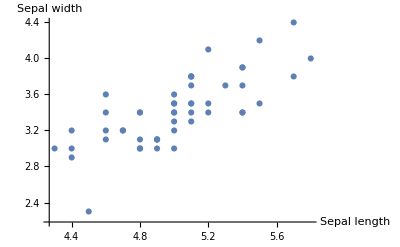

```mathematica
f1=1;
f2=2;
ListPlot[setosaSamples[[All,{f1,f2}]],AxesLabel->features[[{f1,f2}]]]
```

#### Comparing several species

In order to compare several species, it is useful to separate the instances by species

```mathematica
species
```

{Iris-setosa,Iris-versicolor,Iris-virginica}

```mathematica
bySpecies=Cases[irisDataUCI,{___,#}]&/@species;
```

```mathematica
bySpecies
```

{{{5.1,3.5,1.4,0.2,Iris-setosa},{4.9,3.,1.4,0.2,Iris-setosa},{4.7,3.2,1.3,0.2,Iris-setosa},{4.6,3.1,1.5,0.2,Iris-setosa},{5.,3.6,1.4,0.2,Iris-setosa},{5.4,3.9,1.7,0.4,Iris-setosa},{4.6,3.4,1.4,0.3,Iris-setosa},{5.,3.4,1.5,0.2,Iris-setosa},{4.4,2.9,1.4,0.2,Iris-setosa},{4.9,3.1,1.5,0.1,Iris-setosa},{5.4,3.7,1.5,0.2,Iris-setosa},{4.8,3.4,1.6,0.2,Iris-setosa},{4.8,3.,1.4,0.1,Iris-setosa},{4.3,3.,1.1,0.1,Iris-setosa},{5.8,4.,1.2,0.2,Iris-setosa},{5.7,4.4,1.5,0.4,Iris-setosa},{5.4,3.9,1.3,0.4,Iris-setosa},{5.1,3.5,1.4,0.3,Iris-setosa},{5.7,3.8,1.7,0.3,Iris-setosa},{5.1,3.8,1.5,0.3,Iris-setosa},{5.4,3.4,1.7,0.2,Iris-setosa},{5.1,3.7,1.5,0.4,Iris-setosa},{4.6,3.6,1.,0.2,Iris-setosa},{5.1,3.3,1.7,0.5,Iris-setosa},{4.8,3.4,1.9,0.2,Iris-setosa},{5.,3.,1.6,0.2,Iris-setosa},{5.,3.4,1.6,0.4,Iris-setosa},{5.2,3.5,1.5,0.2,Iris-setosa},{5.2,3.4,1.4,0.2,Iris-setosa},{4.7,3.2,1.6,0.2,Iris-setosa},{4.8,3.1,1.6,0.2,Iris-setosa},{5.4,3.4,1.5,0.4,Iris-setosa},{5.2,4.1,1.5,0.1,Iris-setosa},{5.5,4.2,1.4,0.2,Iris-setosa},{4.9,3.1,1.5,0.1,Iris-setosa},{5.,3.2,1.2,0.2,Iris-setosa},{5.5,3.5,1.3,0.2,Iris-setosa},{4.9,3.1,1.5,0.1,Iris-setosa},{4.4,3.,1.3,0.2,Iris-setosa},{5.1,3.4,1.5,0.2,Iris-setosa},{5.,3.5,1.3,0.3,Iris-setosa},{4.5,2.3,1.3,0.3,Iris-setosa},{4.4,3.2,1.3,0.2,Iris-setosa},{5.,3.5,1.6,0.6,Iris-setosa},{5.1,3.8,1.9,0.4,Iris-setosa},{4.8,3.,1.4,0.3,Iris-setosa},{5.1,3.8,1.6,0.2,Iris-setosa},{4.6,3.2,1.4,0.2,Iris-setosa},{5.3,3.7,1.5,0.2,Iris-setosa},{5.,3.3,1.4,0.2,Iris-setosa}},{{7.,3.2,4.7,1.4,Iris-versicolor},{6.4,3.2,4.5,1.5,Iris-versicolor},{6.9,3.1,4.9,1.5,Iris-versicolor},{5.5,2.3,4.,1.3,Iris-versicolor},{6.5,2.8,4.6,1.5,Iris-versicolor},{5.7,2.8,4.5,1.3,Iris-versicolor},{6.3,3.3,4.7,1.6,Iris-versicolor},{4.9,2.4,3.3,1.,Iris-versicolor},{6.6,2.9,4.6,1.3,Iris-versicolor},{5.2,2.7,3.9,1.4,Iris-versicolor},{5.,2.,3.5,1.,Iris-versicolor},{5.9,3.,4.2,1.5,Iris-versicolor},{6.,2.2,4.,1.,Iris-versicolor},{6.1,2.9,4.7,1.4,Iris-versicolor},{5.6,2.9,3.6,1.3,Iris-versicolor},{6.7,3.1,4.4,1.4,Iris-versicolor},{5.6,3.,4.5,1.5,Iris-versicolor},{5.8,2.7,4.1,1.,Iris-versicolor},{6.2,2.2,4.5,1.5,Iris-versicolor},{5.6,2.5,3.9,1.1,Iris-versicolor},{5.9,3.2,4.8,1.8,Iris-versicolor},{6.1,2.8,4.,1.3,Iris-versicolor},{6.3,2.5,4.9,1.5,Iris-versicolor},{6.1,2.8,4.7,1.2,Iris-versicolor},{6.4,2.9,4.3,1.3,Iris-versicolor},{6.6,3.,4.4,1.4,Iris-versicolor},{6.8,2.8,4.8,1.4,Iris-versicolor},{6.7,3.,5.,1.7,Iris-versicolor},{6.,2.9,4.5,1.5,Iris-versicolor},{5.7,2.6,3.5,1.,Iris-versicolor},{5.5,2.4,3.8,1.1,Iris-versicolor},{5.5,2.4,3.7,1.,Iris-versicolor},{5.8,2.7,3.9,1.2,Iris-versicolor},{6.,2.7,5.1,1.6,Iris-versicolor},{5.4,3.,4.5,1.5,Iris-versicolor},{6.,3.4,4.5,1.6,Iris-versicolor},{6.7,3.1,4.7,1.5,Iris-versicolor},{6.3,2.3,4.4,1.3,Iris-versicolor},{5.6,3.,4.1,1.3,Iris-versicolor},{5.5,2.5,4.,1.3,Iris-versicolor},{5.5,2.6,4.4,1.2,Iris-versicolor},{6.1,3.,4.6,1.4,Iris-versicolor},{5.8,2.6,4.,1.2,Iris-versicolor},{5.,2.3,3.3,1.,Iris-versicolor},{5.6,2.7,4.2,1.3,Iris-versicolor},{5.7,3.,4.2,1.2,Iris-versicolor},{5.7,2.9,4.2,1.3,Iris-versicolor},{6.2,2.9,4.3,1.3,Iris-versicolor},{5.1,2.5,3.,1.1,Iris-versicolor},{5.7,2.8,4.1,1.3,Iris-versicolor}},{{6.3,3.3,6.,2.5,Iris-virginica},{5.8,2.7,5.1,1.9,Iris-virginica},{7.1,3.,5.9,2.1,Iris-virginica},{6.3,2.9,5.6,1.8,Iris-virginica},{6.5,3.,5.8,2.2,Iris-virginica},{7.6,3.,6.6,2.1,Iris-virginica},{4.9,2.5,4.5,1.7,Iris-virginica},{7.3,2.9,6.3,1.8,Iris-virginica},{6.7,2.5,5.8,1.8,Iris-virginica},{7.2,3.6,6.1,2.5,Iris-virginica},{6.5,3.2,5.1,2.,Iris-virginica},{6.4,2.7,5.3,1.9,Iris-virginica},{6.8,3.,5.5,2.1,Iris-virginica},{5.7,2.5,5.,2.,Iris-virginica},{5.8,2.8,5.1,2.4,Iris-virginica},{6.4,3.2,5.3,2.3,Iris-virginica},{6.5,3.,5.5,1.8,Iris-virginica},{7.7,3.8,6.7,2.2,Iris-virginica},{7.7,2.6,6.9,2.3,Iris-virginica},{6.,2.2,5.,1.5,Iris-virginica},{6.9,3.2,5.7,2.3,Iris-virginica},{5.6,2.8,4.9,2.,Iris-virginica},{7.7,2.8,6.7,2.,Iris-virginica},{6.3,2.7,4.9,1.8,Iris-virginica},{6.7,3.3,5.7,2.1,Iris-virginica},{7.2,3.2,6.,1.8,Iris-virginica},{6.2,2.8,4.8,1.8,Iris-virginica},{6.1,3.,4.9,1.8,Iris-virginica},{6.4,2.8,5.6,2.1,Iris-virginica},{7.2,3.,5.8,1.6,Iris-virginica},{7.4,2.8,6.1,1.9,Iris-virginica},{7.9,3.8,6.4,2.,Iris-virginica},{6.4,2.8,5.6,2.2,Iris-virginica},{6.3,2.8,5.1,1.5,Iris-virginica},{6.1,2.6,5.6,1.4,Iris-virginica},{7.7,3.,6.1,2.3,Iris-virginica},{6.3,3.4,5.6,2.4,Iris-virginica},{6.4,3.1,5.5,1.8,Iris-virginica},{6.,3.,4.8,1.8,Iris-virginica},{6.9,3.1,5.4,2.1,Iris-virginica},{6.7,3.1,5.6,2.4,Iris-virginica},{6.9,3.1,5.1,2.3,Iris-virginica},{5.8,2.7,5.1,1.9,Iris-virginica},{6.8,3.2,5.9,2.3,Iris-virginica},{6.7,3.3,5.7,2.5,Iris-virginica},{6.7,3.,5.2,2.3,Iris-virginica},{6.3,2.5,5.,1.9,Iris-virginica},{6.5,3.,5.2,2.,Iris-virginica},{6.2,3.4,5.4,2.3,Iris-virginica},{5.9,3.,5.1,1.8,Iris-virginica}}}

Alternatively, one can use Map explicitly as follows:

```mathematica
Map[Cases[irisDataUCI,{___,#}]&,species]
```

{{{5.1,3.5,1.4,0.2,Iris-setosa},{4.9,3.,1.4,0.2,Iris-setosa},{4.7,3.2,1.3,0.2,Iris-setosa},{4.6,3.1,1.5,0.2,Iris-setosa},{5.,3.6,1.4,0.2,Iris-setosa},{5.4,3.9,1.7,0.4,Iris-setosa},{4.6,3.4,1.4,0.3,Iris-setosa},{5.,3.4,1.5,0.2,Iris-setosa},{4.4,2.9,1.4,0.2,Iris-setosa},{4.9,3.1,1.5,0.1,Iris-setosa},{5.4,3.7,1.5,0.2,Iris-setosa},{4.8,3.4,1.6,0.2,Iris-setosa},{4.8,3.,1.4,0.1,Iris-setosa},{4.3,3.,1.1,0.1,Iris-setosa},{5.8,4.,1.2,0.2,Iris-setosa},{5.7,4.4,1.5,0.4,Iris-setosa},{5.4,3.9,1.3,0.4,Iris-setosa},{5.1,3.5,1.4,0.3,Iris-setosa},{5.7,3.8,1.7,0.3,Iris-setosa},{5.1,3.8,1.5,0.3,Iris-setosa},{5.4,3.4,1.7,0.2,Iris-setosa},{5.1,3.7,1.5,0.4,Iris-setosa},{4.6,3.6,1.,0.2,Iris-setosa},{5.1,3.3,1.7,0.5,Iris-setosa},{4.8,3.4,1.9,0.2,Iris-setosa},{5.,3.,1.6,0.2,Iris-setosa},{5.,3.4,1.6,0.4,Iris-setosa},{5.2,3.5,1.5,0.2,Iris-setosa},{5.2,3.4,1.4,0.2,Iris-setosa},{4.7,3.2,1.6,0.2,Iris-setosa},{4.8,3.1,1.6,0.2,Iris-setosa},{5.4,3.4,1.5,0.4,Iris-setosa},{5.2,4.1,1.5,0.1,Iris-setosa},{5.5,4.2,1.4,0.2,Iris-setosa},{4.9,3.1,1.5,0.1,Iris-setosa},{5.,3.2,1.2,0.2,Iris-setosa},{5.5,3.5,1.3,0.2,Iris-setosa},{4.9,3.1,1.5,0.1,Iris-setosa},{4.4,3.,1.3,0.2,Iris-setosa},{5.1,3.4,1.5,0.2,Iris-setosa},{5.,3.5,1.3,0.3,Iris-setosa},{4.5,2.3,1.3,0.3,Iris-setosa},{4.4,3.2,1.3,0.2,Iris-setosa},{5.,3.5,1.6,0.6,Iris-setosa},{5.1,3.8,1.9,0.4,Iris-setosa},{4.8,3.,1.4,0.3,Iris-setosa},{5.1,3.8,1.6,0.2,Iris-setosa},{4.6,3.2,1.4,0.2,Iris-setosa},{5.3,3.7,1.5,0.2,Iris-setosa},{5.,3.3,1.4,0.2,Iris-setosa}},{{7.,3.2,4.7,1.4,Iris-versicolor},{6.4,3.2,4.5,1.5,Iris-versicolor},{6.9,3.1,4.9,1.5,Iris-versicolor},{5.5,2.3,4.,1.3,Iris-versicolor},{6.5,2.8,4.6,1.5,Iris-versicolor},{5.7,2.8,4.5,1.3,Iris-versicolor},{6.3,3.3,4.7,1.6,Iris-versicolor},{4.9,2.4,3.3,1.,Iris-versicolor},{6.6,2.9,4.6,1.3,Iris-versicolor},{5.2,2.7,3.9,1.4,Iris-versicolor},{5.,2.,3.5,1.,Iris-versicolor},{5.9,3.,4.2,1.5,Iris-versicolor},{6.,2.2,4.,1.,Iris-versicolor},{6.1,2.9,4.7,1.4,Iris-versicolor},{5.6,2.9,3.6,1.3,Iris-versicolor},{6.7,3.1,4.4,1.4,Iris-versicolor},{5.6,3.,4.5,1.5,Iris-versicolor},{5.8,2.7,4.1,1.,Iris-versicolor},{6.2,2.2,4.5,1.5,Iris-versicolor},{5.6,2.5,3.9,1.1,Iris-versicolor},{5.9,3.2,4.8,1.8,Iris-versicolor},{6.1,2.8,4.,1.3,Iris-versicolor},{6.3,2.5,4.9,1.5,Iris-versicolor},{6.1,2.8,4.7,1.2,Iris-versicolor},{6.4,2.9,4.3,1.3,Iris-versicolor},{6.6,3.,4.4,1.4,Iris-versicolor},{6.8,2.8,4.8,1.4,Iris-versicolor},{6.7,3.,5.,1.7,Iris-versicolor},{6.,2.9,4.5,1.5,Iris-versicolor},{5.7,2.6,3.5,1.,Iris-versicolor},{5.5,2.4,3.8,1.1,Iris-versicolor},{5.5,2.4,3.7,1.,Iris-versicolor},{5.8,2.7,3.9,1.2,Iris-versicolor},{6.,2.7,5.1,1.6,Iris-versicolor},{5.4,3.,4.5,1.5,Iris-versicolor},{6.,3.4,4.5,1.6,Iris-versicolor},{6.7,3.1,4.7,1.5,Iris-versicolor},{6.3,2.3,4.4,1.3,Iris-versicolor},{5.6,3.,4.1,1.3,Iris-versicolor},{5.5,2.5,4.,1.3,Iris-versicolor},{5.5,2.6,4.4,1.2,Iris-versicolor},{6.1,3.,4.6,1.4,Iris-versicolor},{5.8,2.6,4.,1.2,Iris-versicolor},{5.,2.3,3.3,1.,Iris-versicolor},{5.6,2.7,4.2,1.3,Iris-versicolor},{5.7,3.,4.2,1.2,Iris-versicolor},{5.7,2.9,4.2,1.3,Iris-versicolor},{6.2,2.9,4.3,1.3,Iris-versicolor},{5.1,2.5,3.,1.1,Iris-versicolor},{5.7,2.8,4.1,1.3,Iris-versicolor}},{{6.3,3.3,6.,2.5,Iris-virginica},{5.8,2.7,5.1,1.9,Iris-virginica},{7.1,3.,5.9,2.1,Iris-virginica},{6.3,2.9,5.6,1.8,Iris-virginica},{6.5,3.,5.8,2.2,Iris-virginica},{7.6,3.,6.6,2.1,Iris-virginica},{4.9,2.5,4.5,1.7,Iris-virginica},{7.3,2.9,6.3,1.8,Iris-virginica},{6.7,2.5,5.8,1.8,Iris-virginica},{7.2,3.6,6.1,2.5,Iris-virginica},{6.5,3.2,5.1,2.,Iris-virginica},{6.4,2.7,5.3,1.9,Iris-virginica},{6.8,3.,5.5,2.1,Iris-virginica},{5.7,2.5,5.,2.,Iris-virginica},{5.8,2.8,5.1,2.4,Iris-virginica},{6.4,3.2,5.3,2.3,Iris-virginica},{6.5,3.,5.5,1.8,Iris-virginica},{7.7,3.8,6.7,2.2,Iris-virginica},{7.7,2.6,6.9,2.3,Iris-virginica},{6.,2.2,5.,1.5,Iris-virginica},{6.9,3.2,5.7,2.3,Iris-virginica},{5.6,2.8,4.9,2.,Iris-virginica},{7.7,2.8,6.7,2.,Iris-virginica},{6.3,2.7,4.9,1.8,Iris-virginica},{6.7,3.3,5.7,2.1,Iris-virginica},{7.2,3.2,6.,1.8,Iris-virginica},{6.2,2.8,4.8,1.8,Iris-virginica},{6.1,3.,4.9,1.8,Iris-virginica},{6.4,2.8,5.6,2.1,Iris-virginica},{7.2,3.,5.8,1.6,Iris-virginica},{7.4,2.8,6.1,1.9,Iris-virginica},{7.9,3.8,6.4,2.,Iris-virginica},{6.4,2.8,5.6,2.2,Iris-virginica},{6.3,2.8,5.1,1.5,Iris-virginica},{6.1,2.6,5.6,1.4,Iris-virginica},{7.7,3.,6.1,2.3,Iris-virginica},{6.3,3.4,5.6,2.4,Iris-virginica},{6.4,3.1,5.5,1.8,Iris-virginica},{6.,3.,4.8,1.8,Iris-virginica},{6.9,3.1,5.4,2.1,Iris-virginica},{6.7,3.1,5.6,2.4,Iris-virginica},{6.9,3.1,5.1,2.3,Iris-virginica},{5.8,2.7,5.1,1.9,Iris-virginica},{6.8,3.2,5.9,2.3,Iris-virginica},{6.7,3.3,5.7,2.5,Iris-virginica},{6.7,3.,5.2,2.3,Iris-virginica},{6.3,2.5,5.,1.9,Iris-virginica},{6.5,3.,5.2,2.,Iris-virginica},{6.2,3.4,5.4,2.3,Iris-virginica},{5.9,3.,5.1,1.8,Iris-virginica}}}

```mathematica
Length[bySpecies]
```

3

```mathematica
bySpecies[[3]]
```

{{6.3,3.3,6.,2.5,Iris-virginica},{5.8,2.7,5.1,1.9,Iris-virginica},{7.1,3.,5.9,2.1,Iris-virginica},{6.3,2.9,5.6,1.8,Iris-virginica},{6.5,3.,5.8,2.2,Iris-virginica},{7.6,3.,6.6,2.1,Iris-virginica},{4.9,2.5,4.5,1.7,Iris-virginica},{7.3,2.9,6.3,1.8,Iris-virginica},{6.7,2.5,5.8,1.8,Iris-virginica},{7.2,3.6,6.1,2.5,Iris-virginica},{6.5,3.2,5.1,2.,Iris-virginica},{6.4,2.7,5.3,1.9,Iris-virginica},{6.8,3.,5.5,2.1,Iris-virginica},{5.7,2.5,5.,2.,Iris-virginica},{5.8,2.8,5.1,2.4,Iris-virginica},{6.4,3.2,5.3,2.3,Iris-virginica},{6.5,3.,5.5,1.8,Iris-virginica},{7.7,3.8,6.7,2.2,Iris-virginica},{7.7,2.6,6.9,2.3,Iris-virginica},{6.,2.2,5.,1.5,Iris-virginica},{6.9,3.2,5.7,2.3,Iris-virginica},{5.6,2.8,4.9,2.,Iris-virginica},{7.7,2.8,6.7,2.,Iris-virginica},{6.3,2.7,4.9,1.8,Iris-virginica},{6.7,3.3,5.7,2.1,Iris-virginica},{7.2,3.2,6.,1.8,Iris-virginica},{6.2,2.8,4.8,1.8,Iris-virginica},{6.1,3.,4.9,1.8,Iris-virginica},{6.4,2.8,5.6,2.1,Iris-virginica},{7.2,3.,5.8,1.6,Iris-virginica},{7.4,2.8,6.1,1.9,Iris-virginica},{7.9,3.8,6.4,2.,Iris-virginica},{6.4,2.8,5.6,2.2,Iris-virginica},{6.3,2.8,5.1,1.5,Iris-virginica},{6.1,2.6,5.6,1.4,Iris-virginica},{7.7,3.,6.1,2.3,Iris-virginica},{6.3,3.4,5.6,2.4,Iris-virginica},{6.4,3.1,5.5,1.8,Iris-virginica},{6.,3.,4.8,1.8,Iris-virginica},{6.9,3.1,5.4,2.1,Iris-virginica},{6.7,3.1,5.6,2.4,Iris-virginica},{6.9,3.1,5.1,2.3,Iris-virginica},{5.8,2.7,5.1,1.9,Iris-virginica},{6.8,3.2,5.9,2.3,Iris-virginica},{6.7,3.3,5.7,2.5,Iris-virginica},{6.7,3.,5.2,2.3,Iris-virginica},{6.3,2.5,5.,1.9,Iris-virginica},{6.5,3.,5.2,2.,Iris-virginica},{6.2,3.4,5.4,2.3,Iris-virginica},{5.9,3.,5.1,1.8,Iris-virginica}}

We can plot the sepal length vs sepal width for all species in a single plot

```mathematica
features
```

{Sepal length,Sepal width,Petal length,Petal width}

```mathematica
species
```

{Iris-setosa,Iris-versicolor,Iris-virginica}

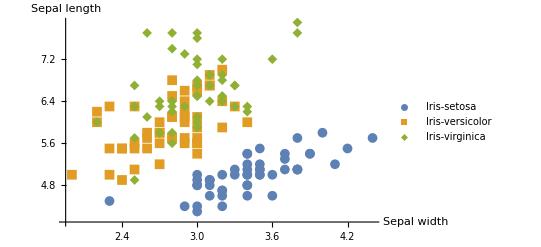

```mathematica
f1=2;
f2=1;
ListPlot[{bySpecies[[1]][[All,{f1,f2}]],bySpecies[[2]][[All,{f1,f2}]],bySpecies[[3]][[All,{f1,f2}]]},AxesLabel->features[[{f1,f2}]],PlotLegends->species,PlotMarkers->{Automatic, Medium}]
```

Varying f1 and f2 between 1 and 4 allows us to plot any feature vs another. 
f  = 1 sepal length
f = 2 sepal width
f = 3 petal length
f = 4 petal width

Try some combinations!

However, it would be useful to have a global view for all pairs of features. This can be achieved by constructing a scatter plot matrix.

#### Scatter Plot Matrix

The scatter plot matrix gives a graphical visualisation of the pair-wise relationship between multiple variables. 

It can be understood as a procedure consisting of several steps:

Create multiple scatter plots to visualize how the sepal length varies with each of sepal width, petal length and petal width. We consider Iris-Setosa as an example:

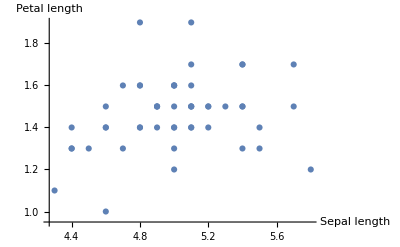
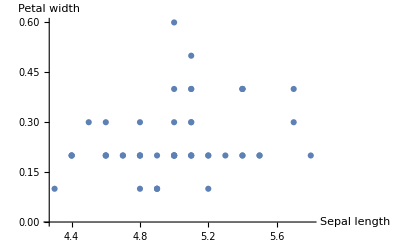
{-Graphics-,-Graphics-,-Graphics-}

```mathematica
ListPlot[bySpecies[[1]][[All,{1,#}]],AxesLabel->{features[[1]],features[[#]]}]&/@{2,3,4}
```

Repeat the above comparison for each variable in turn to create the scatterplot matrix for :

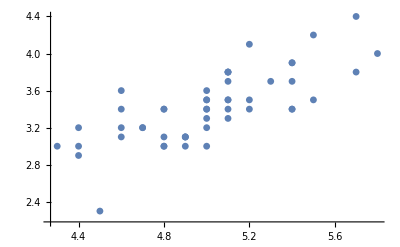
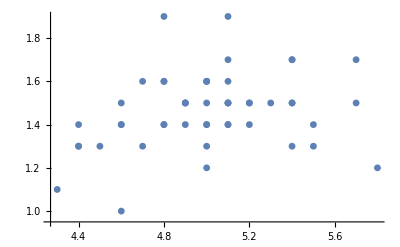
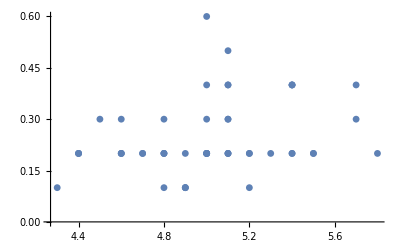
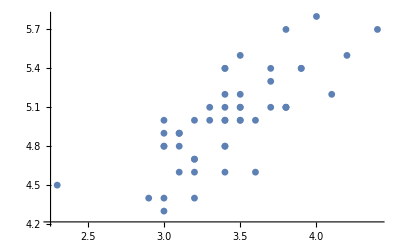
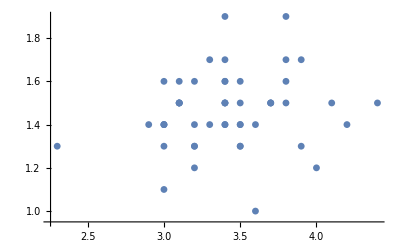
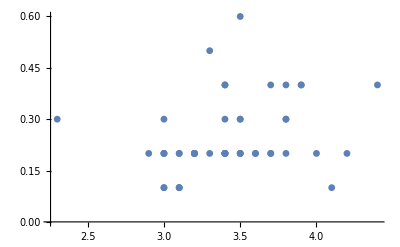
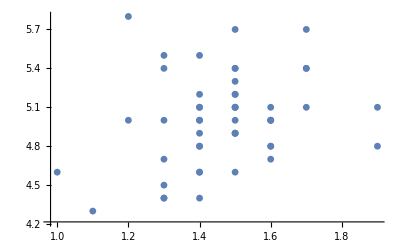
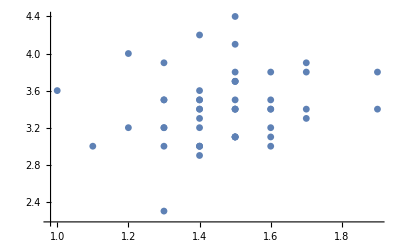
Sepal length | -Graphics- | -Graphics- | -Graphics-
-Graphics- | Sepal width | -Graphics- | -Graphics-
-Graphics- | -Graphics- | Petal length | -Graphics-
-Graphics- | -Graphics- | -Graphics- | Petal width

```mathematica
Table[If[i==j,features[[i]],ListPlot[bySpecies[[1]][[All,{i,j}]],PlotMarkers->{Automatic, Small}]],{i,4},{j,4}]//Grid
```

Plot all the species:

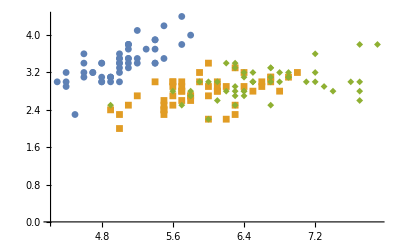
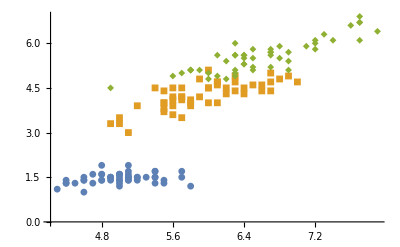
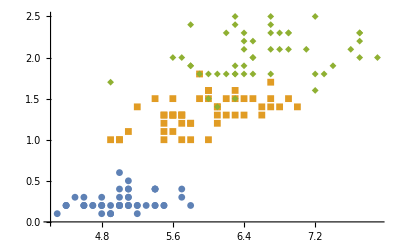
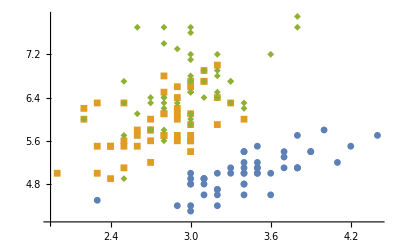
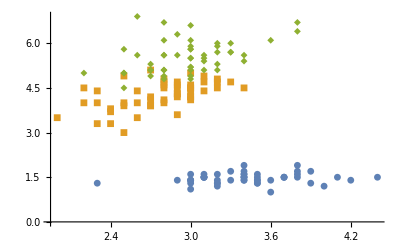
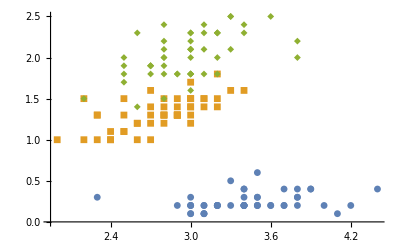
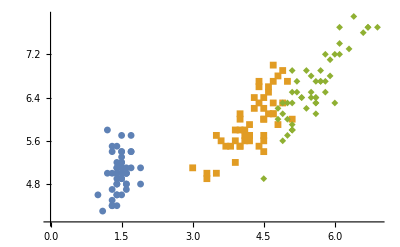
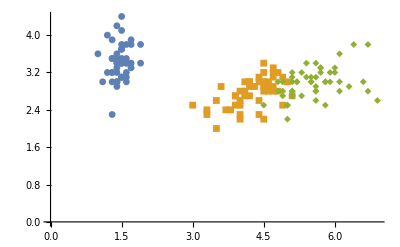
Sepal length | -Graphics- | -Graphics- | -Graphics-
-Graphics- | Sepal width | -Graphics- | -Graphics-
-Graphics- | -Graphics- | Petal length | -Graphics-
-Graphics- | -Graphics- | -Graphics- | Petal width

```mathematica
Table[If[i==j,features[[i]],ListPlot[{bySpecies[[1]][[All,{i,j}]],bySpecies[[2]][[All,{i,j}]],bySpecies[[3]][[All,{i,j}]]},PlotMarkers->{Automatic, Small}]],{i,4},{j,4}]//Grid
```

It looks like the measurements cluster by species. There is hope for a good classification of flower species for unseen samples.

#### A function for the scatter plot matrix:

One can define a function to do scatter plot matrix plots automatically. The inputs for the function are as follows:

values: matrix with values for all features
names: names of the features
vfeatures: vector with the feature number to be plotted 
vclass: vector with class of each instance

```mathematica
ScatterPlotMatrix[values0_,names0_,vfeatures0_,vclass0_]:=Module[{values=values0,names=names0,vf=vfeatures0,vc=vclass0,classes,pos},
classes=DeleteDuplicates[vc];
pos=Table[Flatten[Position[vc,classes[[i]]]],{i,1,Length[classes]}];
Table[If[i==j,names[[i]],ListPlot[Table[Transpose[{values[[pos[[ic]],i]],values[[pos[[ic]],j]]}],{ic,1,Length[classes]}],PlotMarkers->{"OpenMarkers", Small},PlotLegends->DeleteDuplicates[vclass0],PlotRange->All]],{i,vf},{j,vf}]//Grid
]
```

```mathematica
features
```

{Sepal length,Sepal width,Petal length,Petal width}

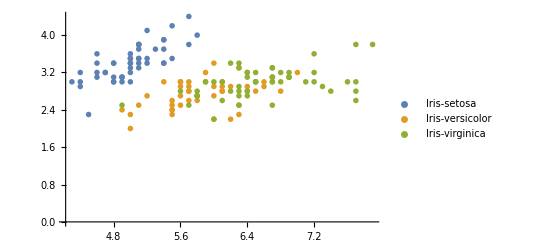
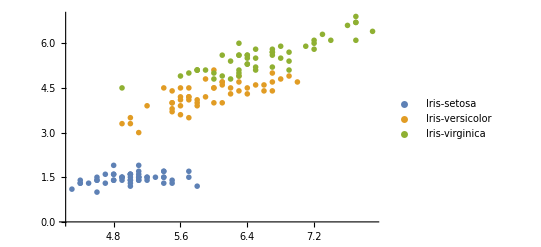
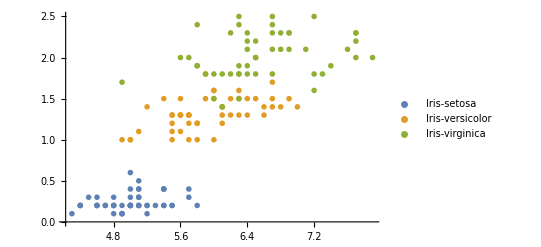
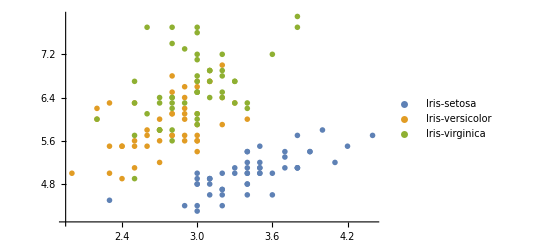
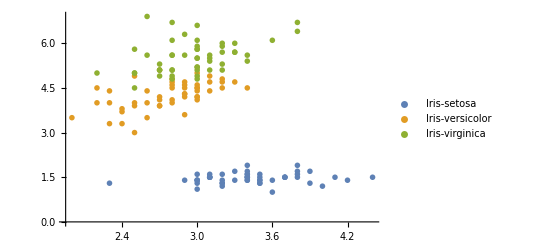
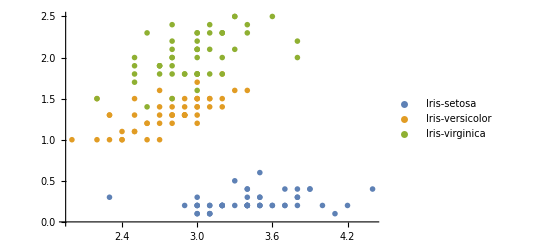
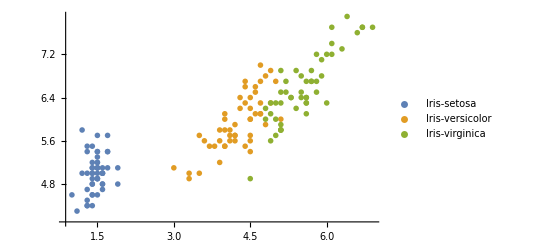
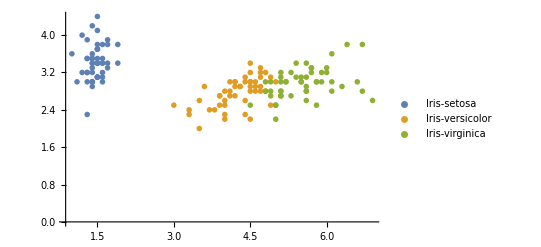
Sepal length | -Graphics- | -Graphics- | -Graphics-
-Graphics- | Sepal width | -Graphics- | -Graphics-
-Graphics- | -Graphics- | Petal length | -Graphics-
-Graphics- | -Graphics- | -Graphics- | Petal width

```mathematica
ScatterPlotMatrix[irisDataUCI[[All,1;;4]],features,{1,2,3,4},irisDataUCI[[All,5]]]
```

Note that this shows a legend for each plot. In some cases with more features, it might be useful not to show the legend if it is clear which symbol corresponds to each class.

An improved function for scatterplot matrix in which legends are only shown once, not in every plot.

```mathematica
ScatterPlotMatrix[values0_,names0_,vfeatures0_,vclass0_]:=Module[{values=values0,names=names0,vf=vfeatures0,vc=vclass0,classes,pos},
classes=DeleteDuplicates[vc];
pos=Table[Flatten[Position[vc,classes[[i]]]],{i,1,Length[classes]}];
Column[
{Table[If[i==j,names[[i]],ListPlot[Table[Transpose[{values[[pos[[ic]],i]],values[[pos[[ic]],j]]}],{ic,1,Length[classes]}],PlotMarkers->{"OpenMarkers", Small},PlotRange->All]],{i,vf},{j,vf}]//Grid,
PointLegend[ColorData[97,"ColorList"][[1;;Length[classes]]],classes,LegendLayout->"Row",LegendMarkers->{"OpenMarkers", Small},LegendFunction->"Frame",LegendLabel->"Classes"]},Alignment->Center
]
]
```

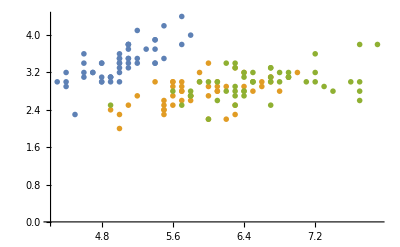
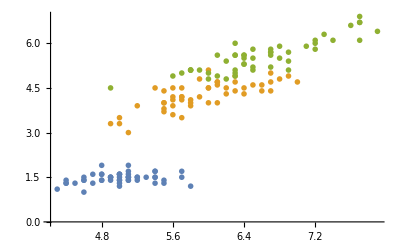
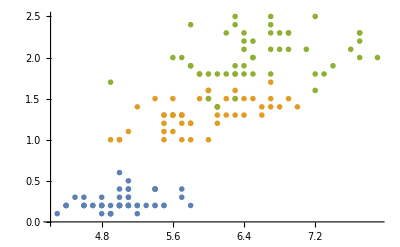
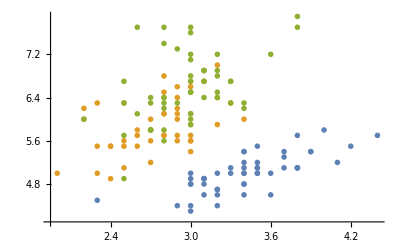
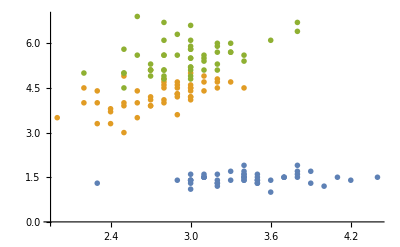
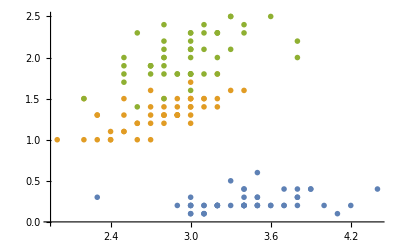
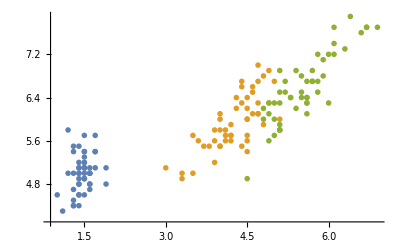
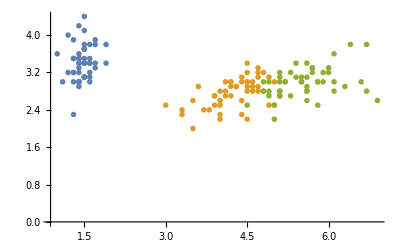
Sepal length | -Graphics- | -Graphics- | -Graphics-
-Graphics- | Sepal width | -Graphics- | -Graphics-
-Graphics- | -Graphics- | Petal length | -Graphics-
-Graphics- | -Graphics- | -Graphics- | Petal width

```mathematica
ScatterPlotMatrix[irisDataUCI[[All,1;;4]],features,{1,2,3,4},irisDataUCI[[All,5]]]
```

Only lower triangular matrix

```mathematica
ScatterPlotMatrixLT[values0_,names0_,vfeatures0_,vclass0_]:=Module[{values=values0,names=names0,vf=vfeatures0,vc=vclass0,classes,pos},
classes=DeleteDuplicates[vc];
pos=Table[Flatten[Position[vc,classes[[i]]]],{i,1,Length[classes]}];
Column[
{Table[If[i==j,names[[i]],If[i>j,ListPlot[Table[Transpose[{values[[pos[[ic]],i]],values[[pos[[ic]],j]]}],{ic,1,Length[classes]}],PlotMarkers->{"OpenMarkers", Small},PlotRange->All]],{}],{i,vf},{j,vf}]//Grid,
PointLegend[ColorData[97,"ColorList"][[1;;Length[classes]]],classes,LegendLayout->"Row",LegendMarkers->{"OpenMarkers", Small},LegendFunction->"Frame",LegendLabel->"Classes"]},Alignment->Center
]
]
```

```mathematica
irisDataUCI
```

{{5.1,3.5,1.4,0.2,Iris-setosa},{4.9,3.,1.4,0.2,Iris-setosa},{4.7,3.2,1.3,0.2,Iris-setosa},{4.6,3.1,1.5,0.2,Iris-setosa},{5.,3.6,1.4,0.2,Iris-setosa},{5.4,3.9,1.7,0.4,Iris-setosa},{4.6,3.4,1.4,0.3,Iris-setosa},{5.,3.4,1.5,0.2,Iris-setosa},{4.4,2.9,1.4,0.2,Iris-setosa},{4.9,3.1,1.5,0.1,Iris-setosa},{5.4,3.7,1.5,0.2,Iris-setosa},{4.8,3.4,1.6,0.2,Iris-setosa},{4.8,3.,1.4,0.1,Iris-setosa},{4.3,3.,1.1,0.1,Iris-setosa},{5.8,4.,1.2,0.2,Iris-setosa},{5.7,4.4,1.5,0.4,Iris-setosa},{5.4,3.9,1.3,0.4,Iris-setosa},{5.1,3.5,1.4,0.3,Iris-setosa},{5.7,3.8,1.7,0.3,Iris-setosa},{5.1,3.8,1.5,0.3,Iris-setosa},{5.4,3.4,1.7,0.2,Iris-setosa},{5.1,3.7,1.5,0.4,Iris-setosa},{4.6,3.6,1.,0.2,Iris-setosa},{5.1,3.3,1.7,0.5,Iris-setosa},{4.8,3.4,1.9,0.2,Iris-setosa},{5.,3.,1.6,0.2,Iris-setosa},{5.,3.4,1.6,0.4,Iris-setosa},{5.2,3.5,1.5,0.2,Iris-setosa},{5.2,3.4,1.4,0.2,Iris-setosa},{4.7,3.2,1.6,0.2,Iris-setosa},{4.8,3.1,1.6,0.2,Iris-setosa},{5.4,3.4,1.5,0.4,Iris-setosa},{5.2,4.1,1.5,0.1,Iris-setosa},{5.5,4.2,1.4,0.2,Iris-setosa},{4.9,3.1,1.5,0.1,Iris-setosa},{5.,3.2,1.2,0.2,Iris-setosa},{5.5,3.5,1.3,0.2,Iris-setosa},{4.9,3.1,1.5,0.1,Iris-setosa},{4.4,3.,1.3,0.2,Iris-setosa},{5.1,3.4,1.5,0.2,Iris-setosa},{5.,3.5,1.3,0.3,Iris-setosa},{4.5,2.3,1.3,0.3,Iris-setosa},{4.4,3.2,1.3,0.2,Iris-setosa},{5.,3.5,1.6,0.6,Iris-setosa},{5.1,3.8,1.9,0.4,Iris-setosa},{4.8,3.,1.4,0.3,Iris-setosa},{5.1,3.8,1.6,0.2,Iris-setosa},{4.6,3.2,1.4,0.2,Iris-setosa},{5.3,3.7,1.5,0.2,Iris-setosa},{5.,3.3,1.4,0.2,Iris-setosa},{7.,3.2,4.7,1.4,Iris-versicolor},{6.4,3.2,4.5,1.5,Iris-versicolor},{6.9,3.1,4.9,1.5,Iris-versicolor},{5.5,2.3,4.,1.3,Iris-versicolor},{6.5,2.8,4.6,1.5,Iris-versicolor},{5.7,2.8,4.5,1.3,Iris-versicolor},{6.3,3.3,4.7,1.6,Iris-versicolor},{4.9,2.4,3.3,1.,Iris-versicolor},{6.6,2.9,4.6,1.3,Iris-versicolor},{5.2,2.7,3.9,1.4,Iris-versicolor},{5.,2.,3.5,1.,Iris-versicolor},{5.9,3.,4.2,1.5,Iris-versicolor},{6.,2.2,4.,1.,Iris-versicolor},{6.1,2.9,4.7,1.4,Iris-versicolor},{5.6,2.9,3.6,1.3,Iris-versicolor},{6.7,3.1,4.4,1.4,Iris-versicolor},{5.6,3.,4.5,1.5,Iris-versicolor},{5.8,2.7,4.1,1.,Iris-versicolor},{6.2,2.2,4.5,1.5,Iris-versicolor},{5.6,2.5,3.9,1.1,Iris-versicolor},{5.9,3.2,4.8,1.8,Iris-versicolor},{6.1,2.8,4.,1.3,Iris-versicolor},{6.3,2.5,4.9,1.5,Iris-versicolor},{6.1,2.8,4.7,1.2,Iris-versicolor},{6.4,2.9,4.3,1.3,Iris-versicolor},{6.6,3.,4.4,1.4,Iris-versicolor},{6.8,2.8,4.8,1.4,Iris-versicolor},{6.7,3.,5.,1.7,Iris-versicolor},{6.,2.9,4.5,1.5,Iris-versicolor},{5.7,2.6,3.5,1.,Iris-versicolor},{5.5,2.4,3.8,1.1,Iris-versicolor},{5.5,2.4,3.7,1.,Iris-versicolor},{5.8,2.7,3.9,1.2,Iris-versicolor},{6.,2.7,5.1,1.6,Iris-versicolor},{5.4,3.,4.5,1.5,Iris-versicolor},{6.,3.4,4.5,1.6,Iris-versicolor},{6.7,3.1,4.7,1.5,Iris-versicolor},{6.3,2.3,4.4,1.3,Iris-versicolor},{5.6,3.,4.1,1.3,Iris-versicolor},{5.5,2.5,4.,1.3,Iris-versicolor},{5.5,2.6,4.4,1.2,Iris-versicolor},{6.1,3.,4.6,1.4,Iris-versicolor},{5.8,2.6,4.,1.2,Iris-versicolor},{5.,2.3,3.3,1.,Iris-versicolor},{5.6,2.7,4.2,1.3,Iris-versicolor},{5.7,3.,4.2,1.2,Iris-versicolor},{5.7,2.9,4.2,1.3,Iris-versicolor},{6.2,2.9,4.3,1.3,Iris-versicolor},{5.1,2.5,3.,1.1,Iris-versicolor},{5.7,2.8,4.1,1.3,Iris-versicolor},{6.3,3.3,6.,2.5,Iris-virginica},{5.8,2.7,5.1,1.9,Iris-virginica},{7.1,3.,5.9,2.1,Iris-virginica},{6.3,2.9,5.6,1.8,Iris-virginica},{6.5,3.,5.8,2.2,Iris-virginica},{7.6,3.,6.6,2.1,Iris-virginica},{4.9,2.5,4.5,1.7,Iris-virginica},{7.3,2.9,6.3,1.8,Iris-virginica},{6.7,2.5,5.8,1.8,Iris-virginica},{7.2,3.6,6.1,2.5,Iris-virginica},{6.5,3.2,5.1,2.,Iris-virginica},{6.4,2.7,5.3,1.9,Iris-virginica},{6.8,3.,5.5,2.1,Iris-virginica},{5.7,2.5,5.,2.,Iris-virginica},{5.8,2.8,5.1,2.4,Iris-virginica},{6.4,3.2,5.3,2.3,Iris-virginica},{6.5,3.,5.5,1.8,Iris-virginica},{7.7,3.8,6.7,2.2,Iris-virginica},{7.7,2.6,6.9,2.3,Iris-virginica},{6.,2.2,5.,1.5,Iris-virginica},{6.9,3.2,5.7,2.3,Iris-virginica},{5.6,2.8,4.9,2.,Iris-virginica},{7.7,2.8,6.7,2.,Iris-virginica},{6.3,2.7,4.9,1.8,Iris-virginica},{6.7,3.3,5.7,2.1,Iris-virginica},{7.2,3.2,6.,1.8,Iris-virginica},{6.2,2.8,4.8,1.8,Iris-virginica},{6.1,3.,4.9,1.8,Iris-virginica},{6.4,2.8,5.6,2.1,Iris-virginica},{7.2,3.,5.8,1.6,Iris-virginica},{7.4,2.8,6.1,1.9,Iris-virginica},{7.9,3.8,6.4,2.,Iris-virginica},{6.4,2.8,5.6,2.2,Iris-virginica},{6.3,2.8,5.1,1.5,Iris-virginica},{6.1,2.6,5.6,1.4,Iris-virginica},{7.7,3.,6.1,2.3,Iris-virginica},{6.3,3.4,5.6,2.4,Iris-virginica},{6.4,3.1,5.5,1.8,Iris-virginica},{6.,3.,4.8,1.8,Iris-virginica},{6.9,3.1,5.4,2.1,Iris-virginica},{6.7,3.1,5.6,2.4,Iris-virginica},{6.9,3.1,5.1,2.3,Iris-virginica},{5.8,2.7,5.1,1.9,Iris-virginica},{6.8,3.2,5.9,2.3,Iris-virginica},{6.7,3.3,5.7,2.5,Iris-virginica},{6.7,3.,5.2,2.3,Iris-virginica},{6.3,2.5,5.,1.9,Iris-virginica},{6.5,3.,5.2,2.,Iris-virginica},{6.2,3.4,5.4,2.3,Iris-virginica},{5.9,3.,5.1,1.8,Iris-virginica}}

```mathematica
ScatterPlotMatrixLT[irisDataUCI[[All,1;;4]],features,{1,2,3,4},irisDataUCI[[All,5]]]
```

Sepal length |  |  | 
-Graphics- | Sepal width |  | 
-Graphics- | -Graphics- | Petal length | 
-Graphics- | -Graphics- | -Graphics- | Petal width

How to read the lower triangular scatterplot matrix?

### Classification analysis

We select a random sample of the dataset that will be used to train a classifier. 

In particular, we select a random set of 20 samples for training:

```mathematica
trainingData=RandomSample[irisDataUCI,20];
```

```mathematica
Tally[trainingData[[All,5]]]
```

{{Iris-versicolor,4},{Iris-setosa,10},{Iris-virginica,6}}

The rest of samples will define a test dataset:

```mathematica
testData=Complement[irisDataUCI,trainingData];
```

```mathematica
Tally[testData[[All,5]]]
```

{{Iris-setosa,38},{Iris-virginica,43},{Iris-versicolor,46}}

```mathematica
CountDistinct[bySpecies[[3]]]
```

Part::partd: Part specification bySpecies⟦3⟧ is longer than depth of object.

2

```mathematica
Length[trainingData]
```

20

```mathematica
Length[testData]
```

127

Check that the training and test datasets are disjoint

```mathematica
Intersection[testData,trainingData]
```

{}

Note that the intersection will not always be the empty set since it might happen that two instances are identical in a dataset (this is not the case in this example)

The classifier can be obtained with the Classify superfunction as follows:

```mathematica
cf=Classify[trainingData[[All,1;;4]]-> trainingData[[All,5]]]
```

ClassifierFunction[…]

### Performance of the classifier on the test data

#### Classifier measurements object

In order to assess the performance of the classifier cf, we will generate a ClassifierMeasurements object. Before doing that, however, we need to get the test data in the right format for the ClassifierMeasurements instruction, i.e. we need to express the test data in the form of an association:

```mathematica
testDataAssoc=Table[testData[[i,1;;4]]->testData[[i,5]],{i,1,Length[testData]}];
```

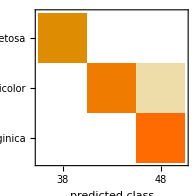
Classifier Measurements
Classifier method | LogisticRegression
Number of test examples | 127
Accuracy | (96.11.7) %
Accuracy baseline | (36.4.) %
Geometric mean of probabilities | 0.853 ± 0.062
Mean cross entropy | 0.159 ± 0.072
Single evaluation time | 1.78 ms/example
Batch evaluation speed | 3.4 examples/ms
-Graphics- |

```mathematica
cm=ClassifierMeasurements[cf,testDataAssoc]
```

One can also define the test data association as follows (check that cm and cm2 give the same results):

```mathematica
testDataAssoc2=testData[[All,1;;4]]->testData[[All,5]];
cm2=ClassifierMeasurements[cf,testDataAssoc2]
```

Classifier Measurements
Classifier method | LogisticRegression
Number of test examples | 127
Accuracy | (96.11.7) %
Accuracy baseline | (36.4.) %
Geometric mean of probabilities | 0.853 ± 0.062
Mean cross entropy | 0.159 ± 0.072
Single evaluation time | 1.88 ms/example
Batch evaluation speed | 3.73 examples/ms
-Graphics- |

The following properties are available for the ClassifierMeasurementsObject  cm:

```mathematica
cm["Properties"]
```

{Accuracy,AccuracyBaseline,AccuracyRejectionPlot,AreaUnderROCCurve,BatchEvaluationTime,BestClassifiedExamples,CalibrationCurve,CalibrationData,ClassifierFunction,ClassMeanCrossEntropy,ClassRejectionRate,CohenKappa,ConfusionDistribution,ConfusionFunction,ConfusionMatrix,ConfusionMatrixPlot,CorrectlyClassifiedExamples,DecisionUtilities,Error,EvaluationTime,Examples,F1Score,FalseDiscoveryRate,FalseNegativeExamples,FalseNegativeNumber,FalseNegativeRate,FalsePositiveExamples,FalsePositiveNumber,FalsePositiveRate,GeometricMeanProbability,IndeterminateExamples,LeastCertainExamples,Likelihood,LinearCalibrationCurve,LogLikelihood,MatthewsCorrelationCoefficient,MeanCrossEntropy,MeanDecisionUtility,MisclassifiedExamples,MostCertainExamples,NegativePredictiveValue,Perplexity,Precision,Probabilities,ProbabilityHistogram,Properties,Recall,RejectionRate,Report,ROCCurve,ROCData,ScottPi,Specificity,TopConfusions,TrueNegativeExamples,TrueNegativeNumber,TruePositiveExamples,TruePositiveNumber,WorstClassifiedExamples}

#### Accuracy

Despite the fact that the training set is quite limited (only 20 instances), the classification is quite accurate:

```mathematica
cm["Accuracy"]
```

0.968504

#### Confusion matrix

The confusion matrix gives a general overview of the performance of the classifier:

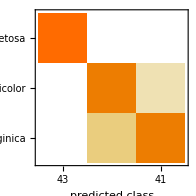

```mathematica
cm["ConfusionMatrixPlot"]
```

In general, classification of Iris-setosa samples is more accurate than for the other two species. 

Iris-versicolor and Iris-virginica are confused with each other more often.

This could be expected from the scatter plot matrix studied above. Indeed, the cluster for Iris-setosa samples is more isolated than those for Iris-versicolor and Iris-virginica.

```mathematica
cm["TrueNegativeNumber"]
```

<|Iris-setosa→85,Iris-versicolor→82,Iris-virginica→82|>

```mathematica
cm["FalsePositiveNumber"]
```

<|Iris-setosa→0,Iris-versicolor→5,Iris-virginica→2|>

```mathematica
cm["FalsePositiveRate"]
```

<|Iris-setosa→0.,Iris-versicolor→0.0574713,Iris-virginica→0.0238095|>

```mathematica
N[8/(41+42)]
```

0.0963855

#### Probabilities of each classification

The probability associated with each prediction is quite high (>0.4) for most instances in the test dataset:

```mathematica
cm["Probabilities"]
```

{0.999896,0.999999,0.582707,0.999939,0.99999,0.999999,1.,0.999982,0.999944,0.998785,0.999017,0.999422,0.999973,0.999859,0.999726,0.997215,0.998879,0.999997,0.999986,0.985,0.999796,0.999892,0.999961,0.999954,0.999996,0.999991,0.999998,0.999696,0.999376,0.999901,0.999983,0.999985,0.999999,1.,0.999999,0.999999,0.998617,0.999826,0.999937,1.,0.984234,0.998666,0.996481,0.999975,0.999999,0.999997,0.999554,1.,1.,0.9999,0.999965,0.999512,1.,0.999963,0.999989,0.999904,0.995854,0.999999,0.999999,0.999994,0.999992,0.999986,0.999803,1.,0.999999,1.,1.,0.999995,0.978873,0.353781,1.,0.669336,0.458754,0.999405,0.806295,0.999696,0.108563,1.,0.999999,0.99993,0.791318,0.971673,0.828838,1.,0.999999,0.999979,0.98425,0.999021,0.903103,0.0053739,0.991757,0.999825,1.,0.998495,0.999997,1.,1.,0.885197,0.999996,0.996399,0.892663,0.999999,0.972019,1.,0.998075,0.991365,0.999995,1.,0.999996,1.,0.999475,1.,0.999653,0.999999,0.999923,0.997439,1.,0.999742,0.0022534,0.233503,1.,0.892872,0.974886,0.999871,1.,0.999564,0.995929,0.0560142}

```mathematica
testData[[All,5]]//TableForm
```

Iris-setosa
Iris-setosa
Iris-setosa
Iris-setosa
Iris-setosa
Iris-setosa
Iris-setosa
Iris-setosa
Iris-setosa
Iris-setosa
Iris-setosa
Iris-setosa
Iris-setosa
Iris-versicolor
Iris-virginica
Iris-setosa
Iris-setosa
Iris-versicolor
Iris-versicolor
Iris-setosa
Iris-setosa
Iris-setosa
Iris-setosa
Iris-setosa
Iris-setosa
Iris-setosa
Iris-setosa
Iris-versicolor
Iris-setosa
Iris-setosa
Iris-setosa
Iris-setosa
Iris-setosa
Iris-setosa
Iris-setosa
Iris-setosa
Iris-versicolor
Iris-setosa
Iris-setosa
Iris-setosa
Iris-versicolor
Iris-setosa
Iris-setosa
Iris-setosa
Iris-setosa
Iris-setosa
Iris-versicolor
Iris-versicolor
Iris-versicolor
Iris-versicolor
Iris-versicolor
Iris-setosa
Iris-versicolor
Iris-versicolor
Iris-virginica
Iris-versicolor
Iris-versicolor
Iris-virginica
Iris-versicolor
Iris-versicolor
Iris-versicolor
Iris-versicolor
Iris-setosa
Iris-setosa
Iris-versicolor
Iris-versicolor
Iris-virginica
Iris-setosa
Iris-virginica
Iris-versicolor
Iris-versicolor
Iris-virginica
Iris-versicolor
Iris-versicolor
Iris-virginica
Iris-versicolor
Iris-virginica
Iris-versicolor
Iris-versicolor
Iris-versicolor
Iris-virginica
Iris-versicolor
Iris-virginica
Iris-versicolor
Iris-virginica
Iris-versicolor
Iris-versicolor
Iris-virginica
Iris-virginica
Iris-virginica
Iris-virginica
Iris-versicolor
Iris-virginica
Iris-virginica
Iris-virginica
Iris-virginica
Iris-versicolor
Iris-virginica
Iris-versicolor
Iris-virginica
Iris-virginica
Iris-virginica
Iris-virginica
Iris-versicolor
Iris-virginica
Iris-versicolor
Iris-virginica
Iris-versicolor
Iris-versicolor
Iris-virginica
Iris-virginica
Iris-virginica
Iris-virginica
Iris-virginica
Iris-virginica
Iris-virginica
Iris-versicolor
Iris-virginica
Iris-virginica
Iris-virginica
Iris-virginica
Iris-virginica
Iris-virginica
Iris-virginica
Iris-virginica
Iris-virginica
Iris-virginica
Iris-virginica

```mathematica
PrependTo
```

PrependTo

```mathematica
Prepend[Transpose[{testData[[All,5]],Table[cf[testData[[i,1;;4]]],{i,1,Length[testData]}],cm["Probabilities"]}],{"True class","Pred class","Probability"}]//TableForm
```

True class | Pred class | Probability
Iris-setosa | Iris-setosa | 0.999896
Iris-setosa | Iris-setosa | 0.999999
Iris-setosa | Iris-setosa | 0.582707
Iris-setosa | Iris-setosa | 0.999939
Iris-setosa | Iris-setosa | 0.99999
Iris-setosa | Iris-setosa | 0.999999
Iris-setosa | Iris-setosa | 1.
Iris-setosa | Iris-setosa | 0.999982
Iris-setosa | Iris-setosa | 0.999944
Iris-setosa | Iris-setosa | 0.998785
Iris-setosa | Iris-setosa | 0.999017
Iris-setosa | Iris-setosa | 0.999422
Iris-setosa | Iris-setosa | 0.999973
Iris-versicolor | Iris-versicolor | 0.999859
Iris-virginica | Iris-virginica | 0.999726
Iris-setosa | Iris-setosa | 0.997215
Iris-setosa | Iris-setosa | 0.998879
Iris-versicolor | Iris-versicolor | 0.999997
Iris-versicolor | Iris-versicolor | 0.999986
Iris-setosa | Iris-setosa | 0.985
Iris-setosa | Iris-setosa | 0.999796
Iris-setosa | Iris-setosa | 0.999892
Iris-setosa | Iris-setosa | 0.999961
Iris-setosa | Iris-setosa | 0.999954
Iris-setosa | Iris-setosa | 0.999996
Iris-setosa | Iris-setosa | 0.999991
Iris-setosa | Iris-setosa | 0.999998
Iris-versicolor | Iris-versicolor | 0.999696
Iris-setosa | Iris-setosa | 0.999376
Iris-setosa | Iris-setosa | 0.999901
Iris-setosa | Iris-setosa | 0.999983
Iris-setosa | Iris-setosa | 0.999985
Iris-setosa | Iris-setosa | 0.999999
Iris-setosa | Iris-setosa | 1.
Iris-setosa | Iris-setosa | 0.999999
Iris-setosa | Iris-setosa | 0.999999
Iris-versicolor | Iris-versicolor | 0.998617
Iris-setosa | Iris-setosa | 0.999826
Iris-setosa | Iris-setosa | 0.999937
Iris-setosa | Iris-setosa | 1.
Iris-versicolor | Iris-versicolor | 0.984234
Iris-setosa | Iris-setosa | 0.998666
Iris-setosa | Iris-setosa | 0.996481
Iris-setosa | Iris-setosa | 0.999975
Iris-setosa | Iris-setosa | 0.999999
Iris-setosa | Iris-setosa | 0.999997
Iris-versicolor | Iris-versicolor | 0.999554
Iris-versicolor | Iris-versicolor | 1.
Iris-versicolor | Iris-versicolor | 1.
Iris-versicolor | Iris-versicolor | 0.9999
Iris-versicolor | Iris-versicolor | 0.999965
Iris-setosa | Iris-setosa | 0.999512
Iris-versicolor | Iris-versicolor | 1.
Iris-versicolor | Iris-versicolor | 0.999963
Iris-virginica | Iris-virginica | 0.999989
Iris-versicolor | Iris-versicolor | 0.999904
Iris-versicolor | Iris-versicolor | 0.995854
Iris-virginica | Iris-virginica | 0.999999
Iris-versicolor | Iris-versicolor | 0.999999
Iris-versicolor | Iris-versicolor | 0.999994
Iris-versicolor | Iris-versicolor | 0.999992
Iris-versicolor | Iris-versicolor | 0.999986
Iris-setosa | Iris-setosa | 0.999803
Iris-setosa | Iris-setosa | 1.
Iris-versicolor | Iris-versicolor | 0.999999
Iris-versicolor | Iris-versicolor | 1.
Iris-virginica | Iris-virginica | 1.
Iris-setosa | Iris-setosa | 0.999995
Iris-virginica | Iris-virginica | 0.978873
Iris-versicolor | Iris-virginica | 0.353781
Iris-versicolor | Iris-versicolor | 1.
Iris-virginica | Iris-virginica | 0.669336
Iris-versicolor | Iris-virginica | 0.458754
Iris-versicolor | Iris-versicolor | 0.999405
Iris-virginica | Iris-virginica | 0.806295
Iris-versicolor | Iris-versicolor | 0.999696
Iris-virginica | Iris-versicolor | 0.108563
Iris-versicolor | Iris-versicolor | 1.
Iris-versicolor | Iris-versicolor | 0.999999
Iris-versicolor | Iris-versicolor | 0.99993
Iris-virginica | Iris-virginica | 0.791318
Iris-versicolor | Iris-versicolor | 0.971673
Iris-virginica | Iris-virginica | 0.828838
Iris-versicolor | Iris-versicolor | 1.
Iris-virginica | Iris-virginica | 0.999999
Iris-versicolor | Iris-versicolor | 0.999979
Iris-versicolor | Iris-versicolor | 0.98425
Iris-virginica | Iris-virginica | 0.999021
Iris-virginica | Iris-virginica | 0.903103
Iris-virginica | Iris-versicolor | 0.0053739
Iris-virginica | Iris-virginica | 0.991757
Iris-versicolor | Iris-versicolor | 0.999825
Iris-virginica | Iris-virginica | 1.
Iris-virginica | Iris-virginica | 0.998495
Iris-virginica | Iris-virginica | 0.999997
Iris-virginica | Iris-virginica | 1.
Iris-versicolor | Iris-versicolor | 1.
Iris-virginica | Iris-virginica | 0.885197
Iris-versicolor | Iris-versicolor | 0.999996
Iris-virginica | Iris-virginica | 0.996399
Iris-virginica | Iris-virginica | 0.892663
Iris-virginica | Iris-virginica | 0.999999
Iris-virginica | Iris-virginica | 0.972019
Iris-versicolor | Iris-versicolor | 1.
Iris-virginica | Iris-virginica | 0.998075
Iris-versicolor | Iris-versicolor | 0.991365
Iris-virginica | Iris-virginica | 0.999995
Iris-versicolor | Iris-versicolor | 1.
Iris-versicolor | Iris-versicolor | 0.999996
Iris-virginica | Iris-virginica | 1.
Iris-virginica | Iris-virginica | 0.999475
Iris-virginica | Iris-virginica | 1.
Iris-virginica | Iris-virginica | 0.999653
Iris-virginica | Iris-virginica | 0.999999
Iris-virginica | Iris-virginica | 0.999923
Iris-virginica | Iris-virginica | 0.997439
Iris-versicolor | Iris-versicolor | 1.
Iris-virginica | Iris-virginica | 0.999742
Iris-virginica | Iris-versicolor | 0.0022534
Iris-virginica | Iris-versicolor | 0.233503
Iris-virginica | Iris-virginica | 1.
Iris-virginica | Iris-virginica | 0.892872
Iris-virginica | Iris-virginica | 0.974886
Iris-virginica | Iris-virginica | 0.999871
Iris-virginica | Iris-virginica | 1.
Iris-virginica | Iris-virginica | 0.999564
Iris-virginica | Iris-virginica | 0.995929
Iris-virginica | Iris-versicolor | 0.0560142

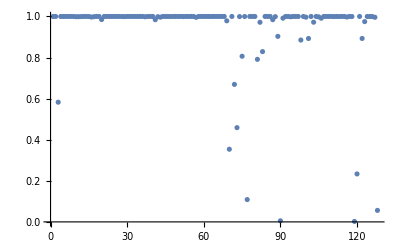

```mathematica
ListPlot[cm["Probabilities"],PlotRange->All]
```

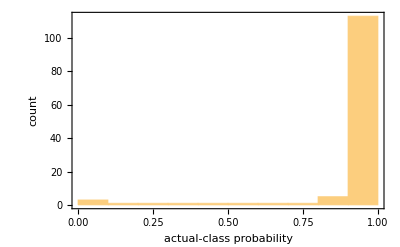

```mathematica
cm["ProbabilityHistogram"]
```

#### Worst classified examples

Iris-virginica and Iris-versicolor samples are the most abundant in the set of worst classified instances.

```mathematica
cm["WorstClassifiedExamples"]
```

{{7.2,3.,5.8,1.6}→Iris-virginica,{6.3,2.8,5.1,1.5}→Iris-virginica,{7.9,3.8,6.4,2.}→Iris-virginica,{6.1,2.6,5.6,1.4}→Iris-virginica,{7.2,3.2,6.,1.8}→Iris-virginica,{5.9,3.2,4.8,1.8}→Iris-versicolor,{6.,2.7,5.1,1.6}→Iris-versicolor,{4.5,2.3,1.3,0.3}→Iris-setosa,{6.,2.2,5.,1.5}→Iris-virginica,{6.1,3.,4.9,1.8}→Iris-virginica}

This can be seen in a more precise manner by constructing a table for the probability of classification of each instance to the right class. 

The following table is sorted in increasing order of probability:

```mathematica
TableForm[SortBy[Transpose[{testData[[All,5]],cm["Probabilities"]}],Last]]
```

Iris-virginica | 0.0022534
Iris-virginica | 0.0053739
Iris-virginica | 0.0560142
Iris-virginica | 0.108563
Iris-virginica | 0.233503
Iris-versicolor | 0.353781
Iris-versicolor | 0.458754
Iris-setosa | 0.582707
Iris-virginica | 0.669336
Iris-virginica | 0.791318
Iris-virginica | 0.806295
Iris-virginica | 0.828838
Iris-virginica | 0.885197
Iris-virginica | 0.892663
Iris-virginica | 0.892872
Iris-virginica | 0.903103
Iris-versicolor | 0.971673
Iris-virginica | 0.972019
Iris-virginica | 0.974886
Iris-virginica | 0.978873
Iris-versicolor | 0.984234
Iris-versicolor | 0.98425
Iris-setosa | 0.985
Iris-versicolor | 0.991365
Iris-virginica | 0.991757
Iris-versicolor | 0.995854
Iris-virginica | 0.995929
Iris-virginica | 0.996399
Iris-setosa | 0.996481
Iris-setosa | 0.997215
Iris-virginica | 0.997439
Iris-virginica | 0.998075
Iris-virginica | 0.998495
Iris-versicolor | 0.998617
Iris-setosa | 0.998666
Iris-setosa | 0.998785
Iris-setosa | 0.998879
Iris-setosa | 0.999017
Iris-virginica | 0.999021
Iris-setosa | 0.999376
Iris-versicolor | 0.999405
Iris-setosa | 0.999422
Iris-virginica | 0.999475
Iris-setosa | 0.999512
Iris-versicolor | 0.999554
Iris-virginica | 0.999564
Iris-virginica | 0.999653
Iris-versicolor | 0.999696
Iris-versicolor | 0.999696
Iris-virginica | 0.999726
Iris-virginica | 0.999742
Iris-setosa | 0.999796
Iris-setosa | 0.999803
Iris-versicolor | 0.999825
Iris-setosa | 0.999826
Iris-versicolor | 0.999859
Iris-virginica | 0.999871
Iris-setosa | 0.999892
Iris-setosa | 0.999896
Iris-versicolor | 0.9999
Iris-setosa | 0.999901
Iris-versicolor | 0.999904
Iris-virginica | 0.999923
Iris-versicolor | 0.99993
Iris-setosa | 0.999937
Iris-setosa | 0.999939
Iris-setosa | 0.999944
Iris-setosa | 0.999954
Iris-setosa | 0.999961
Iris-versicolor | 0.999963
Iris-versicolor | 0.999965
Iris-setosa | 0.999973
Iris-setosa | 0.999975
Iris-versicolor | 0.999979
Iris-setosa | 0.999982
Iris-setosa | 0.999983
Iris-setosa | 0.999985
Iris-versicolor | 0.999986
Iris-versicolor | 0.999986
Iris-virginica | 0.999989
Iris-setosa | 0.99999
Iris-setosa | 0.999991
Iris-versicolor | 0.999992
Iris-versicolor | 0.999994
Iris-virginica | 0.999995
Iris-setosa | 0.999995
Iris-versicolor | 0.999996
Iris-setosa | 0.999996
Iris-versicolor | 0.999996
Iris-virginica | 0.999997
Iris-versicolor | 0.999997
Iris-setosa | 0.999997
Iris-setosa | 0.999998
Iris-setosa | 0.999999
Iris-virginica | 0.999999
Iris-setosa | 0.999999
Iris-virginica | 0.999999
Iris-setosa | 0.999999
Iris-virginica | 0.999999
Iris-versicolor | 0.999999
Iris-versicolor | 0.999999
Iris-virginica | 0.999999
Iris-setosa | 0.999999
Iris-setosa | 0.999999
Iris-setosa | 0.999999
Iris-versicolor | 0.999999
Iris-versicolor | 1.
Iris-virginica | 1.
Iris-versicolor | 1.
Iris-setosa | 1.
Iris-versicolor | 1.
Iris-versicolor | 1.
Iris-versicolor | 1.
Iris-virginica | 1.
Iris-versicolor | 1.
Iris-versicolor | 1.
Iris-virginica | 1.
Iris-versicolor | 1.
Iris-versicolor | 1.
Iris-virginica | 1.
Iris-setosa | 1.
Iris-versicolor | 1.
Iris-setosa | 1.
Iris-virginica | 1.
Iris-versicolor | 1.
Iris-virginica | 1.
Iris-setosa | 1.
Iris-virginica | 1.

#### TPR and FPR

TPR and FPR also suggest that classification of Iris-setosa instances is more precise:

```mathematica
cm["TruePositiveRate"]
```

<|Iris-setosa→1.,Iris-versicolor→0.95122,Iris-virginica→0.886364|>

```mathematica
cm["FalsePositiveRate"]
```

<|Iris-setosa→0.,Iris-versicolor→0.0574713,Iris-virginica→0.0238095|>

#### ROC curves

The ROC curves also suggest that classification of irises from the Setosa species is more precise:

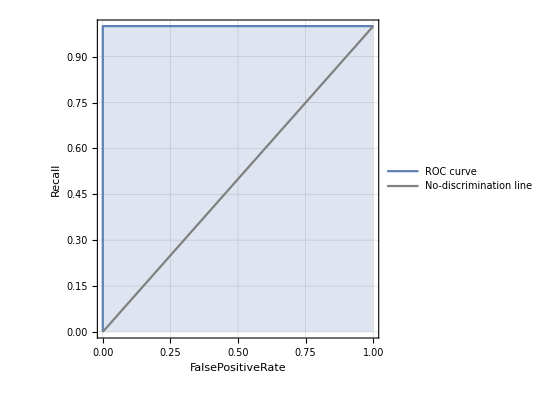
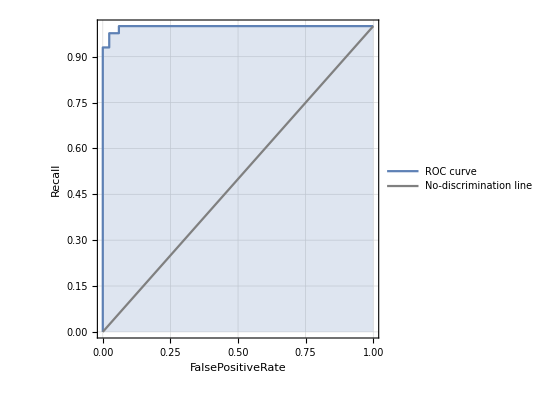
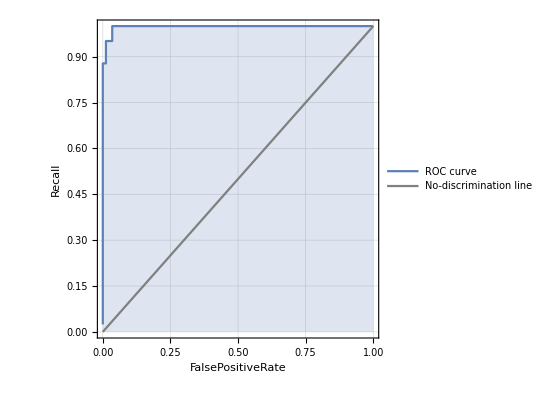
<|Iris-setosa→-Graphics-,Iris-versicolor→-Graphics-,Iris-virginica→-Graphics-|>

```mathematica
cm["ROCCurve"]
```

```mathematica
cm["AreaUnderROCCurve"]
```

<|Iris-setosa→1.,Iris-versicolor→0.997508,Iris-virginica→0.997448|>

#### Potential problems with ROC curves from ClassifierMeasurement objects

Warning: The ROC curve should be a step-wise function in general. However, some new versions of Mathematica do not always get this right (i.e. sometimes it links points in the plot in a non-step-wise manner). In addition, the ROC curve for the third species (last class in the list in general) is not correct. This this the ROC curve for the virginica species which seems to proceed along the random guess line... As a result, the area under the ROC curve is estimated to be 0.5 which is also wrong for this species.

Two functions can be written to calculate the ROC curves and areas under the curve from scratch to solve these issues (you don’t need to understand them in full detail but it is recommended to use these ones in the course):

Function to plot the ROC curve for each class. The inputs are the trained classifier and the test dataset.

```mathematica
ClearAll[ROCcurvePlot];

ROCcurvePlot[classifier_,testData_]:=Module[{classifierIn=classifier,testDataIn=testData},

problist[classifier1_,testDataIn1_,classesIn1_,classi1_]:=Reverse[SortBy[Transpose[{testDataIn1[[All,2]],classifier1[testDataIn1[[All,1]],"Probability"->classesIn[[classi1]]]}],Last]];

ClearAll[tp];
tp[classifier0_,testData0_,classes0_,classi0_]:=Module[{classifierIn0=classifier0,testDataIn0=testData0,classesIn0=classes0,classiIn0=classi0},Reverse[SortBy[Transpose[{testDataIn0[[All,2]],classifierIn0[testDataIn0[[All,1]],"Probability"->classesIn0[[classiIn0]]]}],Last]];
tplist=ConstantArray[0,Length[testDataIn0]];
tplist[[Flatten[Position[problist[classifierIn0,testDataIn0,classesIn0,classiIn0][[All,1]],classesIn0[[classiIn0]]]]]]=1;
tplist
];

classesIn=DeleteDuplicates[testDataIn[[All,2]]];

KeySort[
Association[
Table[
TP=tp[classifierIn,testDataIn,classesIn,i];
FP=ReplaceAll[2->0][TP+1];
tpr=Accumulate[TP]/Total[TP]//N;
fpr=Accumulate[FP]/Total[FP]//N;

classesIn[[i]]->Show[
ListPlot[Prepend[Transpose[{fpr,tpr}],{0,0}],Joined->True,AxesLabel->{"FPR","TPR"},AspectRatio->1,Filling->Bottom,PlotRange->{{0,1},{0,1}}],ListPlot[{{0,0},{1,1}},Joined->True,PlotStyle->{Gray,Dashed}]
]
,{i,1,Length[classesIn]}
]
]
]
]
```

Function for area under the ROC curve

```mathematica
ClearAll[AUC];
(*ClearAll[problist];*)

AUC[classifier_,testData_]:=Module[{classifierIn=classifier,testDataIn=testData},

problist[classifier1_,testDataIn1_,classesIn1_,classi1_]:=Reverse[SortBy[Transpose[{testDataIn1[[All,2]],classifier1[testDataIn1[[All,1]],"Probability"->classesIn[[classi1]]]}],Last]];

ClearAll[tp];
tp[classifier0_,testData0_,classes0_,classi0_]:=Module[{classifierIn0=classifier0,testDataIn0=testData0,classesIn0=classes0,classiIn0=classi0},Reverse[SortBy[Transpose[{testDataIn0[[All,2]],classifierIn0[testDataIn0[[All,1]],"Probability"->classesIn0[[classiIn0]]]}],Last]];
tplist=ConstantArray[0,Length[testDataIn0]];
tplist[[Flatten[Position[problist[classifierIn0,testDataIn0,classesIn0,classiIn0][[All,1]],classesIn0[[classiIn0]]]]]]=1;
tplist
];

classesIn=DeleteDuplicates[testDataIn[[All,2]]];

KeySort[
Association[
Table[
TP=tp[classifierIn,testDataIn,classesIn,i];
FP=ReplaceAll[2->0][TP+1];
tpr=Accumulate[TP]/Total[TP]//N;
fpr=Accumulate[FP]/Total[FP]//N;

aux=Prepend[Transpose[{fpr,tpr}],{0,0}];

classesIn[[i]]->Total[Table[(aux[[j+1,1]]-aux[[j,1]])*aux[[j+1,2]],{j,1,Length[aux]-1}]]

,{i,1,Length[classesIn]}
]
]
]
]
```

The area under the curve is:

```mathematica
AUC[cf,testDataAssoc]
```

<|Iris-setosa→1.,Iris-versicolor→0.997508,Iris-virginica→0.997448|>

Compare with the results obtained with ClassifierMeasurements:

```mathematica
cm["AreaUnderROCCurve"]
```

<|Iris-setosa→1.,Iris-versicolor→0.997508,Iris-virginica→0.997448|>

As expected, the area for Iris-virginica is quite different.

This corresponds to differences in the ROC curves:

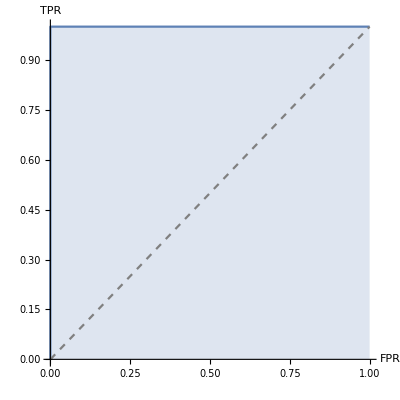
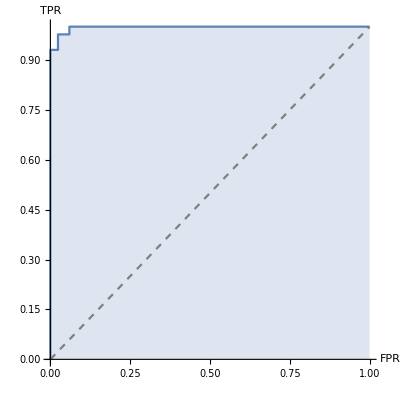
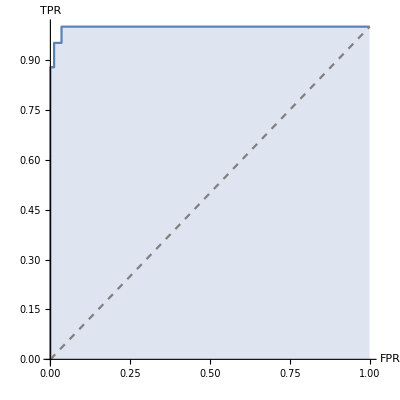
<|Iris-setosa→-Graphics-,Iris-versicolor→-Graphics-,Iris-virginica→-Graphics-|>

```mathematica
ROCcurvePlot[cf,testDataAssoc]
```

Compare with the curves obtained with ClassifierMeasurements:

```mathematica
cm["ROCCurve"]
```

<|Iris-setosa→-Graphics-,Iris-versicolor→-Graphics-,Iris-virginica→-Graphics-|>

#### Probability that an example is classified to a certain class

For instance, for class 1.

```mathematica
species[[1]]
```

Iris-setosa

```mathematica
cf[testDataAssoc[[All,1]],"Probability"->species[[1]]]
```

{0.999896,0.999999,0.582707,0.999939,0.99999,0.999999,1.,0.999982,0.999944,0.998785,0.999017,0.999422,0.999973,0.000141078,3.45029×10^-9,0.997215,0.998879,9.67301×10^-8,0.0000136702,0.985,0.999796,0.999892,0.999961,0.999954,0.999996,0.999991,0.999998,0.000304196,0.999376,0.999901,0.999983,0.999985,0.999999,1.,0.999999,0.999999,0.000087882,0.999826,0.999937,1.,0.000100247,0.998666,0.996481,0.999975,0.999999,0.999997,1.21687×10^-8,1.11808×10^-7,8.50619×10^-8,1.99083×10^-7,1.58568×10^-7,0.999512,9.22046×10^-8,5.97059×10^-7,3.85872×10^-12,0.0000952612,0.0000155714,1.82016×10^-15,5.99836×10^-7,1.38296×10^-6,3.82602×10^-6,0.000013913,0.999803,1.,4.35504×10^-8,2.5745×10^-7,1.42922×10^-17,0.999995,2.80118×10^-9,2.39622×10^-6,2.02111×10^-11,2.55199×10^-13,2.91359×10^-10,9.10693×10^-8,3.14322×10^-8,0.000109581,6.64522×10^-12,4.76443×10^-8,3.00401×10^-9,1.50236×10^-8,9.07649×10^-9,7.68378×10^-13,2.60713×10^-10,2.41694×10^-8,1.34422×10^-12,1.48095×10^-12,4.41747×10^-12,4.59573×10^-15,9.78234×10^-12,1.38173×10^-10,9.54327×10^-13,7.62869×10^-7,1.22626×10^-14,1.45002×10^-14,4.57251×10^-17,3.69807×10^-18,3.71044×10^-9,1.24497×10^-10,1.42038×10^-7,1.46144×10^-12,1.12775×10^-11,3.04521×10^-17,2.71498×10^-10,1.82365×10^-10,9.1895×10^-18,9.59662×10^-11,4.57052×10^-16,2.77692×10^-9,9.88691×10^-10,6.82155×10^-18,3.60705×10^-13,1.54403×10^-17,3.02048×10^-15,3.11627×10^-17,6.00022×10^-15,5.15542×10^-14,2.1626×10^-10,2.94972×10^-17,3.8469×10^-14,2.79745×10^-13,5.54×10^-17,7.41537×10^-17,4.00233×10^-18,9.5605×10^-21,5.07426×10^-28,4.76283×10^-22,6.4368×10^-15,5.78694×10^-13}

One can look at the probability that any example is classified as Iris-setosa and the actual classification. A true positive for setosa is observed when an example from this species is classified into setosa. When examples from other species are classified to setosa as the probability threshold decreases, one registers false positives for setosa.

```mathematica
TableForm[Transpose[{testDataAssoc[[All,2]],cf[testDataAssoc[[All,1]],"Probability"->species[[1]]]}]]
```

Iris-setosa | 0.999896
Iris-setosa | 0.999999
Iris-setosa | 0.582707
Iris-setosa | 0.999939
Iris-setosa | 0.99999
Iris-setosa | 0.999999
Iris-setosa | 1.
Iris-setosa | 0.999982
Iris-setosa | 0.999944
Iris-setosa | 0.998785
Iris-setosa | 0.999017
Iris-setosa | 0.999422
Iris-setosa | 0.999973
Iris-versicolor | 0.000141078
Iris-virginica | 3.45029×10^-9
Iris-setosa | 0.997215
Iris-setosa | 0.998879
Iris-versicolor | 9.67301×10^-8
Iris-versicolor | 0.0000136702
Iris-setosa | 0.985
Iris-setosa | 0.999796
Iris-setosa | 0.999892
Iris-setosa | 0.999961
Iris-setosa | 0.999954
Iris-setosa | 0.999996
Iris-setosa | 0.999991
Iris-setosa | 0.999998
Iris-versicolor | 0.000304196
Iris-setosa | 0.999376
Iris-setosa | 0.999901
Iris-setosa | 0.999983
Iris-setosa | 0.999985
Iris-setosa | 0.999999
Iris-setosa | 1.
Iris-setosa | 0.999999
Iris-setosa | 0.999999
Iris-versicolor | 0.000087882
Iris-setosa | 0.999826
Iris-setosa | 0.999937
Iris-setosa | 1.
Iris-versicolor | 0.000100247
Iris-setosa | 0.998666
Iris-setosa | 0.996481
Iris-setosa | 0.999975
Iris-setosa | 0.999999
Iris-setosa | 0.999997
Iris-versicolor | 1.21687×10^-8
Iris-versicolor | 1.11808×10^-7
Iris-versicolor | 8.50619×10^-8
Iris-versicolor | 1.99083×10^-7
Iris-versicolor | 1.58568×10^-7
Iris-setosa | 0.999512
Iris-versicolor | 9.22046×10^-8
Iris-versicolor | 5.97059×10^-7
Iris-virginica | 3.85872×10^-12
Iris-versicolor | 0.0000952612
Iris-versicolor | 0.0000155714
Iris-virginica | 1.82016×10^-15
Iris-versicolor | 5.99836×10^-7
Iris-versicolor | 1.38296×10^-6
Iris-versicolor | 3.82602×10^-6
Iris-versicolor | 0.000013913
Iris-setosa | 0.999803
Iris-setosa | 1.
Iris-versicolor | 4.35504×10^-8
Iris-versicolor | 2.5745×10^-7
Iris-virginica | 1.42922×10^-17
Iris-setosa | 0.999995
Iris-virginica | 2.80118×10^-9
Iris-versicolor | 2.39622×10^-6
Iris-versicolor | 2.02111×10^-11
Iris-virginica | 2.55199×10^-13
Iris-versicolor | 2.91359×10^-10
Iris-versicolor | 9.10693×10^-8
Iris-virginica | 3.14322×10^-8
Iris-versicolor | 0.000109581
Iris-virginica | 6.64522×10^-12
Iris-versicolor | 4.76443×10^-8
Iris-versicolor | 3.00401×10^-9
Iris-versicolor | 1.50236×10^-8
Iris-virginica | 9.07649×10^-9
Iris-versicolor | 7.68378×10^-13
Iris-virginica | 2.60713×10^-10
Iris-versicolor | 2.41694×10^-8
Iris-virginica | 1.34422×10^-12
Iris-versicolor | 1.48095×10^-12
Iris-versicolor | 4.41747×10^-12
Iris-virginica | 4.59573×10^-15
Iris-virginica | 9.78234×10^-12
Iris-virginica | 1.38173×10^-10
Iris-virginica | 9.54327×10^-13
Iris-versicolor | 7.62869×10^-7
Iris-virginica | 1.22626×10^-14
Iris-virginica | 1.45002×10^-14
Iris-virginica | 4.57251×10^-17
Iris-virginica | 3.69807×10^-18
Iris-versicolor | 3.71044×10^-9
Iris-virginica | 1.24497×10^-10
Iris-versicolor | 1.42038×10^-7
Iris-virginica | 1.46144×10^-12
Iris-virginica | 1.12775×10^-11
Iris-virginica | 3.04521×10^-17
Iris-virginica | 2.71498×10^-10
Iris-versicolor | 1.82365×10^-10
Iris-virginica | 9.1895×10^-18
Iris-versicolor | 9.59662×10^-11
Iris-virginica | 4.57052×10^-16
Iris-versicolor | 2.77692×10^-9
Iris-versicolor | 9.88691×10^-10
Iris-virginica | 6.82155×10^-18
Iris-virginica | 3.60705×10^-13
Iris-virginica | 1.54403×10^-17
Iris-virginica | 3.02048×10^-15
Iris-virginica | 3.11627×10^-17
Iris-virginica | 6.00022×10^-15
Iris-virginica | 5.15542×10^-14
Iris-versicolor | 2.1626×10^-10
Iris-virginica | 2.94972×10^-17
Iris-virginica | 3.8469×10^-14
Iris-virginica | 2.79745×10^-13
Iris-virginica | 5.54×10^-17
Iris-virginica | 7.41537×10^-17
Iris-virginica | 4.00233×10^-18
Iris-virginica | 9.5605×10^-21
Iris-virginica | 5.07426×10^-28
Iris-virginica | 4.76283×10^-22
Iris-virginica | 6.4368×10^-15
Iris-virginica | 5.78694×10^-13

Sorting these probabilities it hopefully finds that most setosa have been classified to this species with high probability:

```mathematica
TableForm[Reverse[SortBy[Transpose[{testDataAssoc[[All,2]],cf[testDataAssoc[[All,1]],"Probability"->species[[1]]]}],Last]]]
```

Iris-setosa | 1.
Iris-setosa | 1.
Iris-setosa | 1.
Iris-setosa | 1.
Iris-setosa | 0.999999
Iris-setosa | 0.999999
Iris-setosa | 0.999999
Iris-setosa | 0.999999
Iris-setosa | 0.999999
Iris-setosa | 0.999999
Iris-setosa | 0.999998
Iris-setosa | 0.999997
Iris-setosa | 0.999996
Iris-setosa | 0.999995
Iris-setosa | 0.999991
Iris-setosa | 0.99999
Iris-setosa | 0.999985
Iris-setosa | 0.999983
Iris-setosa | 0.999982
Iris-setosa | 0.999975
Iris-setosa | 0.999973
Iris-setosa | 0.999961
Iris-setosa | 0.999954
Iris-setosa | 0.999944
Iris-setosa | 0.999939
Iris-setosa | 0.999937
Iris-setosa | 0.999901
Iris-setosa | 0.999896
Iris-setosa | 0.999892
Iris-setosa | 0.999826
Iris-setosa | 0.999803
Iris-setosa | 0.999796
Iris-setosa | 0.999512
Iris-setosa | 0.999422
Iris-setosa | 0.999376
Iris-setosa | 0.999017
Iris-setosa | 0.998879
Iris-setosa | 0.998785
Iris-setosa | 0.998666
Iris-setosa | 0.997215
Iris-setosa | 0.996481
Iris-setosa | 0.985
Iris-setosa | 0.582707
Iris-versicolor | 0.000304196
Iris-versicolor | 0.000141078
Iris-versicolor | 0.000109581
Iris-versicolor | 0.000100247
Iris-versicolor | 0.0000952612
Iris-versicolor | 0.000087882
Iris-versicolor | 0.0000155714
Iris-versicolor | 0.000013913
Iris-versicolor | 0.0000136702
Iris-versicolor | 3.82602×10^-6
Iris-versicolor | 2.39622×10^-6
Iris-versicolor | 1.38296×10^-6
Iris-versicolor | 7.62869×10^-7
Iris-versicolor | 5.99836×10^-7
Iris-versicolor | 5.97059×10^-7
Iris-versicolor | 2.5745×10^-7
Iris-versicolor | 1.99083×10^-7
Iris-versicolor | 1.58568×10^-7
Iris-versicolor | 1.42038×10^-7
Iris-versicolor | 1.11808×10^-7
Iris-versicolor | 9.67301×10^-8
Iris-versicolor | 9.22046×10^-8
Iris-versicolor | 9.10693×10^-8
Iris-versicolor | 8.50619×10^-8
Iris-versicolor | 4.76443×10^-8
Iris-versicolor | 4.35504×10^-8
Iris-virginica | 3.14322×10^-8
Iris-versicolor | 2.41694×10^-8
Iris-versicolor | 1.50236×10^-8
Iris-versicolor | 1.21687×10^-8
Iris-virginica | 9.07649×10^-9
Iris-versicolor | 3.71044×10^-9
Iris-virginica | 3.45029×10^-9
Iris-versicolor | 3.00401×10^-9
Iris-virginica | 2.80118×10^-9
Iris-versicolor | 2.77692×10^-9
Iris-versicolor | 9.88691×10^-10
Iris-versicolor | 2.91359×10^-10
Iris-virginica | 2.71498×10^-10
Iris-virginica | 2.60713×10^-10
Iris-versicolor | 2.1626×10^-10
Iris-versicolor | 1.82365×10^-10
Iris-virginica | 1.38173×10^-10
Iris-virginica | 1.24497×10^-10
Iris-versicolor | 9.59662×10^-11
Iris-versicolor | 2.02111×10^-11
Iris-virginica | 1.12775×10^-11
Iris-virginica | 9.78234×10^-12
Iris-virginica | 6.64522×10^-12
Iris-versicolor | 4.41747×10^-12
Iris-virginica | 3.85872×10^-12
Iris-versicolor | 1.48095×10^-12
Iris-virginica | 1.46144×10^-12
Iris-virginica | 1.34422×10^-12
Iris-virginica | 9.54327×10^-13
Iris-versicolor | 7.68378×10^-13
Iris-virginica | 5.78694×10^-13
Iris-virginica | 3.60705×10^-13
Iris-virginica | 2.79745×10^-13
Iris-virginica | 2.55199×10^-13
Iris-virginica | 5.15542×10^-14
Iris-virginica | 3.8469×10^-14
Iris-virginica | 1.45002×10^-14
Iris-virginica | 1.22626×10^-14
Iris-virginica | 6.4368×10^-15
Iris-virginica | 6.00022×10^-15
Iris-virginica | 4.59573×10^-15
Iris-virginica | 3.02048×10^-15
Iris-virginica | 1.82016×10^-15
Iris-virginica | 4.57052×10^-16
Iris-virginica | 7.41537×10^-17
Iris-virginica | 5.54×10^-17
Iris-virginica | 4.57251×10^-17
Iris-virginica | 3.11627×10^-17
Iris-virginica | 3.04521×10^-17
Iris-virginica | 2.94972×10^-17
Iris-virginica | 1.54403×10^-17
Iris-virginica | 1.42922×10^-17
Iris-virginica | 9.1895×10^-18
Iris-virginica | 6.82155×10^-18
Iris-virginica | 4.00233×10^-18
Iris-virginica | 3.69807×10^-18
Iris-virginica | 9.5605×10^-21
Iris-virginica | 4.76283×10^-22
Iris-virginica | 5.07426×10^-28